# Import MC Data and inputs from Blines

```mathematica
Get["NeutronBeam/ManualShift_NBeamInt.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["NeutronBeam/XYBinIntBoundaries.m"]
```

```mathematica
MCFolder="~/ClusterMC_v4/NoMoS_Danfysik_25-02-19_reduceTypes_smallerDV4/";
```

```mathematica
DetHisto=Import[MCFolder<>"GlobalTransferData/"<>"DetXYHistSum.txt","Table"]
```

{{-0.07,-0.065,-0.06,-0.055,-0.05,-0.045,-0.04,-0.035,-0.03,-0.025,-0.02,-0.015,-0.01,-0.005,1.38778×10^-17,0.005,0.01,0.015,0.02,0.025,0.03,0.035,0.04,0.045},{-1.054,-1.049,-1.044,-1.039,-1.034,-1.029,-1.024,-1.019,-1.014,-1.009,-1.004,-0.999002,-0.994002,-0.989002,-0.984002,-0.979002,-0.974002,-0.969002,-0.964002,-0.959002,-0.954002,-0.949002,-0.944002},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0},{0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0},{0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0},{0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0},{0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0},{0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0},{0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0},{0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0},{0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0},{0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0},{0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0},{0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0},{0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0},{0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0},{0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0},{0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0},{0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0},{0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
DetTable=Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,2]]-DetHisto[[1,1]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,2]]-DetHisto[[2,1]])/2)-R,
DetHisto[[2+i,j]]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1];
```

### import other parameters

```mathematica
{{MeanX,MeanY},{ApertX,ApertY},{BDV},{BF},{BA},{BRxB},{BDet}}=Import[MCFolder<>"GlobalTransferData/"<>"OtherParas.txt","Table"]
```

{{0.0301277,1.00623},{0.01,0.035},{0.220899},{0.451107},{0.219769},{0.219722},{0.207816}}

### we take the apert offset from the MC extraction

```mathematica
ApertXOff=0.03;ApertYOff=0.;
```

```mathematica
rF=BF/BDV
rA=BA/BDV
rRxB=BRxB/BDV
rDet=BDet/BRxB
```

2.04214

0.994887

0.994674

0.945816

### grab alpha from blines

```mathematica
AlphaFromBlines=178.20869281586448/180*Pi
```

3.11033

### actually, thDet is also different due to alpha not doing 180°!

```mathematica
(*YBlineShiftatDet=-0.016078000000000037;*)
```

```mathematica
BRxBCenterFromBLines=0.21957007943037976;
```

```mathematica
(BRxBCenterFromBLines-BRxB)/BRxBCenterFromBLines
```

-0.000691704

### difference is 7e-4. as the MC value is the average over all particles, it doesnt represent the model description. Model needs BRxB in geometric center of beam (actually geometric tube)

```mathematica
XAShift=0.0;
```

```mathematica
YAShift=0.007188045691239971;
```

```mathematica
YRxBShift=0.00677284727516161;
```

```mathematica
YDetShift=0.015928000000000164;
```

```mathematica
XRxBShift=0.;
```

```mathematica
XDetShift=0.;
```

```mathematica
InfoFile=Import[MCFolder<>"info.txt","Table"];
```

```mathematica
R=InfoFile[[1,2]]
```

0.999002

```mathematica
(*ApertYOff=ApertYOff-R*)
```

### also, we havent considered a shift at detector due to field lines shifting..

```mathematica
ListPlot3D[{#[[1]],#[[2]],#[[3]]/Total[DetTable[[All,3]]]}&/@DetTable,PlotRange->All,InterpolationOrder->1]
```

-Graphics3D-

### boolean plot to see, where > 0

```mathematica
ListPlot3D[Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,1]]-DetHisto[[1,2]])/2,
DetHisto[[2,j]]+(DetHisto[[2,1]]-DetHisto[[2,2]])/2,
Boole[DetHisto[[2+i,j]]>0]},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}
],1],PlotRange->All]
```

-Graphics3D-

### bin step size

```mathematica
-(DetHisto[[1,1]]-DetHisto[[1,2]])
```

0.005

### we can directly get a XYBin form from original table, even being able to jump over steps by 2 e.g.

```mathematica
XYBinBoundariesOriginal=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+1]]},
{-DetHisto[[2,yi+1]]-R,-DetHisto[[2,yi]]-R}
},{xi,1,Length[DetHisto[[1]]]-1},{yi,1,Length[DetHisto[[2]]]-1}],1];
```

```mathematica
XYBinBoundariesOriginal//Length
```

506

## half bins

```mathematica
XYBinBoundariesHalf=Flatten[Table[
{
{DetHisto[[1,xi]],DetHisto[[1,xi+2]]},
{-DetHisto[[2,yi+2]]-R,-DetHisto[[2,yi]]-R}
},{xi,2,Length[DetHisto[[1]]]-2,2},{yi,1,Length[DetHisto[[2]]]-2,2}],1];
```

### we start for x at index 2 for shift, also because that area is 0 anyway

```mathematica
XYBinBoundariesHalf//Length
```

121

```mathematica
(506-22)/4.
```

121.

```mathematica
XYBinBoundariesHalf[[1]]
```

{{-0.065,-0.055},{0.045,0.055}}

```mathematica
XYBinCentersHalf=BinCenters[XYBinBoundariesHalf];
```

```mathematica
a
```

### plot center points of bins

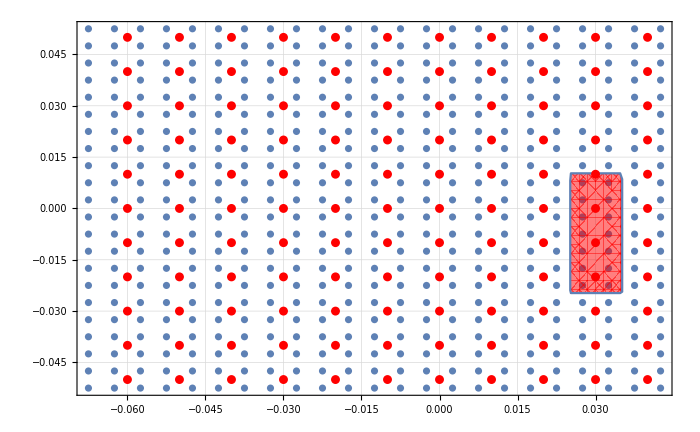

```mathematica
Show[
ListPlot[
Flatten[Table[
{
DetHisto[[1,i]]+(DetHisto[[1,2]]-DetHisto[[1,1]])/2,
-(DetHisto[[2,j]]+(DetHisto[[2,2]]-DetHisto[[2,1]])/2)-R
},
{i,1,Length[DetHisto[[1]]]-1},
{j,1,Length[DetHisto[[2]]]-1}],1],PlotRange->All],
RegionPlot[Abs[x-ApertXOff]<ApertX/2&&Abs[y+ApertYOff]<ApertY/2,{x,0,0.06},{y,-0.05,0.05},PlotStyle->Directive[Red,Opacity[0.5]]],
ListPlot[XYBinCentersHalf,PlotStyle->Red]
]
```

### now we still have to adopt the MC data to half binning

### sum the next neighbouring entries

```mathematica
DetHisto[[2+10,5]]+DetHisto[[2+10+1,5]]+DetHisto[[2+10,6]]+DetHisto[[2+10+1,6]]
```

15823

```mathematica
DetHistoBinHalfEntries=Flatten[Table[

DetHisto[[2+xi,yj]]+DetHisto[[2+xi,yj+1]]+DetHisto[[2+xi+1,yj]]+DetHisto[[2+xi+1,yj+1]],
{xi,2,Length[DetHisto[[1]]]-2,2},
{yj,1,Length[DetHisto[[2]]]-2,2}],1]
```

{0,0,0,0,0,0,0,0,0,0,0,0,2,40,119,142,126,75,13,0,0,0,0,108,796,1846,2370,2057,1208,321,17,0,0,4,666,4796,12351,15200,13717,8107,2318,159,0,0,2,1877,15823,50672,62798,58277,33986,7254,455,0,0,2,2377,32479,119667,146391,140010,82674,13509,362,0,0,0,965,38633,175070,210254,207450,121204,13181,47,0,0,0,35,25350,161013,186172,189699,111325,5414,0,0,0,0,0,7093,76815,84945,88555,52117,443,0,0,0,0,0,386,9415,9711,10374,6182,0,0,0,0,0,0,0,4,1,1,5,0,0,0,0}

```mathematica
Show[

ListPlot3D[{#[[1]],#[[2]],#[[3]]/Total[DetTable[[All,3]]]}&/@DetTable,PlotRange->All,PlotStyle->Directive[Opacity[0.5],Red],InterpolationOrder->1],

ListPlot3D[Transpose[{XYBinCentersHalf[[All,1]],XYBinCentersHalf[[All,2]],DetHistoBinHalfEntries/Total[DetHistoBinHalfEntries]/3.9}],PlotRange->All,InterpolationOrder->1,PlotStyle->Directive[Opacity[0.5],Blue]]
]
```

-Graphics3D-

# Get b0 from raw energy fit

```mathematica
EHisto={{0,19550,39100,58650,78200,97750,117300,136850,156400,175950,195500,215050,234600,254150,273700,293250,312800,332350,351900,371450,391000,410550,430100,449650,469200,488750,508300,527850,547400,566950,586500,606050,625600,645150,664700,684250,703800,723350,742900,762450,782000},{346513,594262,752207,876257,976772,1057642,1125859,1180669,1225108,1257819,1280816,1294590,1300669,1294235,1281846,1262522,1235139,1200930,1159120,1116025,1064817,1009259,948177,884889,817021,747223,679132,606469,536427,465628,396264,329609,266697,208156,153816,107114,66949,35323,13249,1940}};
```

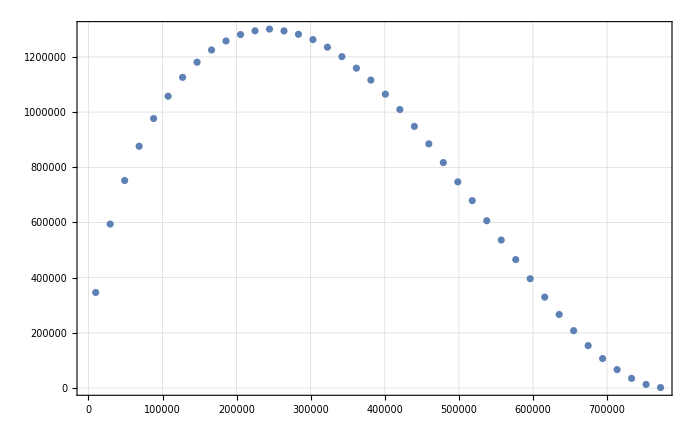

```mathematica
ListPlot[Transpose[{EHisto[[1,1;;-2]]+EHisto[[1,2]]/2,Around[#,Sqrt[#]]&/@EHisto[[2]]}]]
```

```mathematica
FitData=Table[{bin,EHisto[[2,bin]]},{bin,1,Length[EHisto[[2]]]}]
```

{{1,346513},{2,594262},{3,752207},{4,876257},{5,976772},{6,1057642},{7,1125859},{8,1180669},{9,1225108},{10,1257819},{11,1280816},{12,1294590},{13,1300669},{14,1294235},{15,1281846},{16,1262522},{17,1235139},{18,1200930},{19,1159120},{20,1116025},{21,1064817},{22,1009259},{23,948177},{24,884889},{25,817021},{26,747223},{27,679132},{28,606469},{29,536427},{30,465628},{31,396264},{32,329609},{33,266697},{34,208156},{35,153816},{36,107114},{37,66949},{38,35323},{39,13249},{40,1940}}

```mathematica
GlobalStat=Total[EHisto[[2]]]
```

31157159

```mathematica
CloseKernels[]
LaunchKernels[4]
```

{}

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local],KernelObject[4,local]}

```mathematica
ClearAll[eSpectrumBinned]
```

```mathematica
eSpectrumBinned[b_?NumericQ]:=eSpectrumBinned[b]=GlobalStat*ParallelTable[
NIntegrate[weNormed[λ0,κ0,b,Ee],{Ee,me+EHisto[[1,bin]],me+EHisto[[1,bin+1]]},PrecisionGoal->6],{bin,1,Length[EHisto[[1]]]-1}]
```

```mathematica
ClearAll[eSpectrumBin]
```

```mathematica
eSpectrumBin[b_?NumericQ,bin_?NumericQ]:=eSpectrumBinned[b][[bin]]
```

```mathematica
eSpectrumBin[0.,1]
```

345381.

```mathematica
Total[Table[eSpectrumBin[0.,bin],{bin,1,Length[EHisto[[1]]]-1}]]
```

3.11572×10^7

```mathematica
rawSpecFit=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.6<b<0.6},
{{b,0.5}},
bin,
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.000324095,bin]]

### takes 6 min

```mathematica
rawSpecFit["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.000324095 | 0.00121154 | -0.267506 | 0.790489

### now with statistical weights included

```mathematica
rawSpecFitWeights=NonlinearModelFit[
FitData,
{eSpectrumBin[b,bin],-0.005<b<0.005},
{{b,0.0001}},
bin,Weights->1/FitData[[All,2]],VarianceEstimatorFunction->(1&),
Method->"NMinimize",PrecisionGoal->6
]
```

FittedModel[eSpectrumBin[-0.0000338264,bin]]

```mathematica
365/60.
```

6.08333

### takes 6 min

```mathematica
rawSpecFitWeights["ParameterTable"]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
b | -0.0000338264 | 0.00134066 | -0.0252311 | 0.979999

```mathematica
rawSpecFitWeights["BestFitParameters"][[1,2]]//ScientificForm
```

-3.38264×10^-5

```mathematica
Sqrt[GlobalStat]*0.00134
```

7.47969

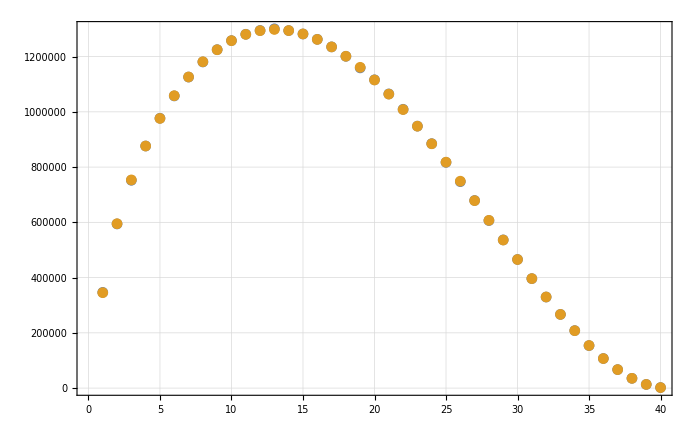

```mathematica
ListPlot[{FitData,Table[rawSpecFitWeights[bin],{bin,1,40}]}]
```

# Test the transfer function

```mathematica
IntMethod={"GlobalAdaptive",Method->"MultidimensionalRule"};
```

## original bin size

### transfer normally takes 21h for 10 cores

```mathematica
XYBinCentersOriginal=BinCenters[XYBinBoundariesOriginal];
```

### MC in Contour plot

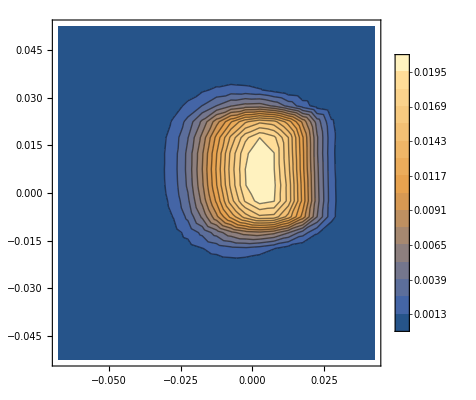

```mathematica
ListContourPlot[Transpose[{XYBinCentersOriginal[[All,1]],XYBinCentersOriginal[[All,2]],DetTable[[All,3]]/Total[DetTable[[All,3]]]}],PlotRange->All,Contours->15,PlotLegends->Automatic]
```

### we now get new Transfer calc from G PC, using the correct aperture cut (the one which the MC actually used, not MeanXA,MeanYA, but the manually chosen cut!)

```mathematica
Part1={{10.6418, 0.}, {10.6548, 0.}, {10.6862, 0.}, {10.7654, 0.}, {11.1106,
   0.}, {11.1335, 0.}, {11.166, 0.}, {11.0654, 0.}, {10.9281, 
  0.}, {11.1535, 0.}, {11.0262, 0.}, {11.1506, 0.}, {11.4254, 
  0.}, {11.1986, 0.}, {10.9406, 0.}, {10.7858, 0.}, {10.8266, 
  0.}, {10.8889, 0.}, {10.9968, 0.}, {11.1072, 0.}, {9.87142, 
  0.}, {9.93609, 0.}, {9.44894, 0.}, {9.36974, 0.}, {9.58728, 
  0.}, {9.21603, 0.}, {9.13213, 2.33772*10^-11}, {9.65344, 
  2.68694*10^-10}, {9.54942, 3.23702*10^-10}, {9.67547, 
  1.02102*10^-10}, {9.7146, 1.49681*10^-11}, {9.56424, 
  4.19215*10^-13}, {9.49899, 0.}, {9.34226, 0.}, {9.67064, 
  0.}, {9.58769, 0.}, {9.17396, 0.}, {8.97512, 0.}, {8.92691, 
  0.}, {8.98998, 0.}, {9.00302, 0.}, {9.11178, 0.}, {9.11219, 
  0.}, {9.11549, 0.}, {9.41545, 0.}, {9.28491, 0.}, {9.19162, 
  0.}, {31.0296, 6.35715*10^-9}, {125.51, 7.27306*10^-8}, {194.877, 
  2.1172*10^-7}, {193.949, 3.28993*10^-7}, {202.043, 
  3.3141*10^-7}, {189.715, 2.68952*10^-7}, {164.899, 
  2.07354*10^-7}, {167.82, 1.55199*10^-7}, {146.408, 
  1.10869*10^-7}, {132.373, 6.13698*10^-8}, {78.9548, 
  2.0272*10^-8}, {24.4898, 1.49667*10^-9}, {9.69615, 
  1.02329*10^-15}, {9.48321, 0.}, {9.52169, 0.}, {9.4502, 
  0.}, {9.49633, 0.}, {9.62623, 0.}, {9.30342, 0.}, {10.5137, 
  0.}, {10.412, 0.}, {20.3753, 5.62435*10^-9}, {233.609, 
  5.79203*10^-7}, {412.727, 2.28703*10^-6}, {466., 
  4.97713*10^-6}, {599.245, 7.44528*10^-6}, {587.163, 
  8.5008*10^-6}, {550.481, 8.12684*10^-6}, {494.541, 
  7.10887*10^-6}, {502.845, 6.04057*10^-6}, {460.153, 
  4.71559*10^-6}, {454.138, 2.98399*10^-6}, {334.253, 
  1.34577*10^-6}, {195.605, 3.46586*10^-7}, {44.4843, 
  1.1954*10^-8}, {9.54544, 0.}, {9.50554, 0.}, {9.49233, 
  0.}, {9.64365, 0.}, {9.65952, 0.}, {9.74, 0.}, {11.6402, 
  0.}, {20.1958, 1.015*10^-8}, {149.293, 1.32669*10^-6}, {471.654, 
  6.57547*10^-6}, {827.641, 0.0000192648}, {1090., 
  0.00003729}, {1320.16, 0.0000544598}, {1578.3, 
  0.0000645774}, {1253.47, 0.0000659246}, {1330.27, 
  0.0000615129}, {1196.5, 0.0000542882}, {1183.61, 
  0.0000432082}, {944.494, 0.0000292118}, {814.788, 
  0.0000154012}, {518.824, 5.54747*10^-6}, {203.115, 
  8.68758*10^-7}, {24.9862, 1.15026*10^-8}, {10.8112, 0.}, {10.6064, 
  0.}, {10.3583, 0.}, {10.3115, 0.}, {10.4395, 0.}, {12.3979, 
  0.}, {72.3221, 8.16125*10^-7}, {298.279, 9.61134*10^-6}, {556.793, 
  0.0000345336}, {1025.88, 0.0000875597}, {1636.65, 
  0.000159365}, {2037.46, 0.000229254}, {2265.88, 
  0.000276286}, {2100.82, 0.000292127}, {2219.45, 
  0.000281671}, {2451.48, 0.000251573}, {2288.55, 
  0.000203919}, {2002.61, 0.000143062}, {1558.63, 
  0.0000816899}, {985.631, 0.0000347477}, {535.406, 
  9.6637*10^-6}, {103.218, 1.50021*10^-6}, {11.6302, 0.}, {11.8263, 
  0.}, {11.9023, 0.}, {11.9482, 0.}, {11.8454, 0.}, {15.1952, 
  0.}, {176.545, 2.38842*10^-6}, {607.194, 0.0000308526}, {691.612, 
  0.000116963}, {1107.55, 0.000277158}, {2227.87, 
  0.000491302}, {2404.34, 0.000703474}, {2421.69, 
  0.000853948}, {2951.13, 0.000918773}, {2776.51, 
  0.000901503}, {2194.97, 0.000813202}, {2119.15, 
  0.000666596}, {2274.64, 0.000477896}, {1923.46, 
  0.000284917}, {1113.19, 0.000132086}, {620.511, 
  0.0000422347}, {380.827, 7.76488*10^-6}, {12.6811, 
  3.14245*10^-11}, {12.6732, 0.}, {12.5561, 0.}, {12.4086, 
  0.}, {12.5457, 0.}, {20.2191, 0.}, {270.405, 
  7.2379*10^-6}, {987.706, 0.0000841397}, {1136.16, 
  0.000298679}, {1642.26, 0.000693358}, {2219.65, 
  0.00124081}, {2550.96, 0.00179528}, {2763.42, 0.00218139}, {3157.68,
   0.00235936}, {3359.81, 0.00233329}, {2510.82, 
  0.00212113}, {2227.36, 0.00175507}, {2603.14, 0.00127248}, {1857.06,
   0.000767458}, {1167.96, 0.000367831}, {854.086, 
  0.000126764}, {659.428, 0.0000237346}, {15.4783, 
  5.77396*10^-11}, {15.0541, 0.}, {14.8199, 0.}, {14.7636, 
  0.}, {14.3079, 0.}, {23.0711, 0.}, {269.056, 
  0.0000111944}, {1172.32, 0.000174721}, {1582.89, 
  0.000618614}, {2053.11, 0.00146097}, {2309.44, 0.002769}, {2449.28, 
  0.00418904}, {3670.74, 0.00504355}, {3630.55, 0.00542241}, {3943.75,
   0.00537287}, {3569.93, 0.00492377}, {2930.93, 
  0.00412876}, {2467.67, 0.00300569}, {1764.22, 0.00174243}, {1227.91,
   0.000830048}, {1120.12, 0.000293421}, {697.516, 
  0.000057934}, {20.2416, 4.61425*10^-11}, {20.1063, 0.}, {20.0954, 
  0.}, {19.7385, 0.}, {19.8368, 0.}, {26.3088, 0.}, {104.321, 
  7.56103*10^-7}, {1338.96, 0.000287205}, {2074.05, 
  0.00108122}, {2082.23, 0.00265443}, {2166.16, 0.00550046}, {4465.06,
   0.00885148}, {3718.67, 0.0105482}, {4215.94, 0.011275}, {5624.42, 
  0.0112077}, {3960.57, 0.0103927}, {4303.23, 0.00888486}, {2610.93, 
  0.00651043}, {2059.22, 0.0034519}, {1976.56, 0.00157502}, {1593.92, 
  0.000549368}, {898.472, 0.00010247}, {22.6145, 0.}, {22.3836, 
  0.}, {22.0263, 0.}, {22.0857, 0.}, {22.304, 0.}, {26.7701, 
  0.}, {26.5081, 0.}, {1291.01, 0.000342895}, {2423.28, 
  0.00160658}, {2677.68, 0.00420986}, {3086.92, 0.00949463}, {4661.01,
   0.0160812}, {4944.52, 0.0190972}, {4808.21, 0.0203817}, {5689.63, 
  0.0203713}, {4418.63, 0.019122}, {5097.39, 0.0166737}, {4027.79, 
  0.0123221}, {2577.55, 0.00596874}, {2590.03, 0.00257963}, {1983.71, 
  0.000852402}, {913.415, 0.000125187}, {26.016, 0.}, {25.9616, 
  0.}, {25.7701, 0.}, {25.9422, 0.}, {25.5987, 0.}, {26.9527, 
  0.}, {26.8431, 0.}, {856.237, 0.000273845}, {2257.16, 
  0.00203595}, {2550.18, 0.00584574}, {3701.49, 0.0142125}, {5278.02, 
  0.0250026}, {5439.87, 0.0297168}};
```

```mathematica
Part2={{5879.15, 0.0317284}, {6425.47, 0.031873}, {5475.47, 
  0.0302507}, {5632.95, 0.0267643}, {5180.55, 0.019882}, {3071.25, 
  0.00900715}, {2613.04, 0.00366748}, {2078.75, 0.00109242}, {424.109,
   0.0000503312}, {26.3436, 0.}, {26.6975, 0.}, {26.8019, 
  0.}, {26.7562, 0.}, {26.948, 0.}, {26.5976, 0.}, {26.602, 
  0.}, {429.663, 0.0000984542}, {2674.31, 0.00211351}, {2927.94, 
  0.00710511}, {3929.51, 0.0187327}, {6408.66, 0.0340257}, {6306.91, 
  0.0405561}, {5621.11, 0.0432589}, {4889.54, 0.0435489}, {5808.01, 
  0.0418211}, {6552.84, 0.0374034}, {5261.27, 0.0278116}, {2902.05, 
  0.0119766}, {3178.21, 0.00447543}, {1846.84, 0.00105604}, {26.4228, 
  0.}, {26.7431, 0.}, {26.8344, 0.}, {26.7727, 0.}, {26.6693, 
  0.}, {26.4369, 0.}, {26.4129, 0.}, {26.6381, 0.}, {26.5827, 
  0.}, {1697.35, 0.00161714}, {2814.88, 0.00742081}, {3691.95, 
  0.0218713}, {6337.61, 0.0411919}, {5644.13, 0.0492402}, {4729.29, 
  0.0522277}, {3435.11, 0.0525514}, {5076.01, 0.0512519}, {5151., 
  0.0463277}, {4673.76, 0.0343846}, {3284.55, 0.0139284}};
```

```mathematica
Part3={{2721.38, 0.0046037}, {920.666, 0.000719656}, {27.0823, 
  0.}, {26.7893, 0.}, {27.0902, 0.}, {26.7069, 0.}, {26.3337, 
  0.}, {26.5725, 0.}, {25.9866, 0.}, {25.9302, 0.}, {25.998, 
  0.}, {825.487, 0.00073121}, {2544.12, 0.00646227}, {4010.47, 
  0.0225487}, {6620.06, 0.0445134}, {5188.78, 0.0531858}, {3232.25, 
  0.0557097}, {2399.15, 0.0560484}, {3683.98, 0.0556413}, {5621.49, 
  0.05107}, {4540.98, 0.037767}, {3796.54, 0.0140721}, {2645.89, 
  0.00375208}, {327.514, 0.000164503}, {26.0692, 0.}, {26.5326, 
  0.}, {26.4457, 0.}, {26.2956, 0.}, {26.3703, 0.}, {26.6205, 
  0.}, {26.119, 0.}, {26.0667, 0.}, {25.7616, 0.}, {319.958, 
  0.000157449}, {2234.84, 0.00441414}, {4027.1, 0.0203112}, {5506.81, 
  0.0426668}, {3584.74, 0.0504801}, {1747.36, 0.0520222}, {1563.25, 
  0.0524175}, {2238.8, 0.0526636}, {3928.29, 0.0496455}, {4876.2, 
  0.036651}, {2672.75, 0.0120292}, {1677.42, 0.0021456}, {25.5351, 
  0.}, {25.6907, 0.}, {25.7099, 0.}, {25.663, 0.}, {25.6486, 
  0.}, {25.6914, 0.}, {25.8154, 0.}, {25.6591, 0.}, {25.4905, 
  0.}, {25.6419, 0.}, {25.6394, 0.}, {1722.1, 0.00212622}, {3624.33, 
  0.0156155}, {4335.33, 0.035581}, {2761.72, 0.0410279}, {1569.17, 
  0.0417774}, {1594.41, 0.0422275}, {1942.59, 0.0426667}, {3312.2, 
  0.0415183}, {3923.33, 0.0308507}, {2572.08, 0.00830736}, {791.995, 
  0.000691064}, {25.8394, 0.}, {25.6641, 0.}, {25.4227, 0.}, {25.6229,
   0.}, {25.3866, 0.}, {25.3937, 0.}, {25.8012, 0.}, {25.702, 
  0.}, {25.4554, 0.}, {25.4368, 0.}, {25.7419, 0.}, {897.853, 
  0.000645083}, {2590.21, 0.00972676}, {2864.66, 0.0245961}, {1189.75,
   0.0272447}, {926.679, 0.0276236}, {930.514, 0.0279821}, {935.543, 
  0.0283461}, {2169.22, 0.028312}, {3248.41, 0.0215837}, {2196.56, 
  0.004253}, {352.231, 0.0000991444}, {25.8784, 0.}, {25.3696, 
  0.}, {25.5892, 0.}, {25.913, 0.}, {25.2089, 0.}, {25.6129, 
  0.}, {25.3513, 0.}, {25.3054, 0.}, {25.4504, 0.}, {25.6937, 
  0.}, {25.408, 0.}, {249.716, 0.0000671335}, {2202.57, 0.00444243},
  {2374.62, 0.0126323}, {912.675, 0.0134189}, {871.475, 
  0.0136123}, {868.756, 0.0138093}, {867.497, 0.0140102}, {1380.7, 
  0.0141814}, {2747.7, 0.0113256}, {1669.1, 0.00138303}, {25.1351, 
  0.}, {25.6959, 0.}, {25.3281, 0.}, {25.4945, 0.}, {25.5488, 
  0.}, {25.4414, 0.}, {25.7181, 0.}, {25.4445, 0.}, {18.9554, 
  0.}, {18.4642, 0.}, {19.0099, 0.}, {18.9648, 0.}, {19.3024, 
  0.}, {1537.53, 0.000564643}, {2085.03, 0.00177238}, {1422.15, 
  0.00185311}, {1428.12, 0.00188724}, {1453.69, 0.0019222}, {1455.36, 
  0.00195802}, {1531.47, 0.00199461}, {2259.78, 0.00164241}, {726.883,
   0.000143063}, {18.7749, 0.}, {18.5465, 0.}, {18.9208, 
  0.}, {18.4023, 0.}, {18.6178, 0.}, {18.6554, 0.}, {18.4987, 
  0.}, {18.5535, 0.}, {17.1697, 0.}, {17.2163, 0.}, {17.1466, 
  0.}, {17.5339, 0.}, {17.9264, 0.}, {565.877, 
  0.0000477822}, {668.649, 0.000158958}, {692.199, 
  0.000162454}, {708.576, 0.000165747}, {729.368, 
  0.000169128}, {757.542, 0.000172598}, {763.698, 
  0.00017616}, {946.399, 0.000154275}, {298.374, 
  4.8665*10^-6}, {17.6567, 0.}, {17.3491, 0.}, {17.2869, 
  0.}, {17.1332, 0.}, {17.5982, 0.}, {17.2737, 0.}, {17.2913, 
  0.}, {17.478, 0.}, {13.0536, 0.}, {13.1281, 0.}, {13.1683, 
  0.}, {13.2287, 0.}, {13.7388, 0.}, {19.0946, 
  2.38871*10^-8}, {29.2692, 1.54622*10^-7}, {28.4156, 
  1.57389*10^-7}, {28.3234, 1.60225*10^-7}, {28.1848, 
  1.63132*10^-7}, {28.4803, 1.66111*10^-7}, {28.8299, 
  1.69165*10^-7}, {27.1581, 1.48771*10^-7}, {14.0612, 0.}, {13.2067, 
  0.}, {13.0134, 0.}, {12.9935, 0.}, {12.8777, 0.}, {13.2731, 
  0.}, {12.8974, 0.}, {12.8731, 0.}, {13.0032, 0.}, {11.3405, 
  0.}, {11.3753, 0.}, {11.3468, 0.}, {11.6981, 0.}, {11.9611, 
  0.}, {12.8006, 0.}, {12.9668, 0.}, {12.7138, 0.}, {12.5912, 
  0.}, {12.4534, 0.}, {12.4761, 0.}, {12.6179, 0.}, {12.9897, 
  0.}, {12.3665, 0.}, {11.8331, 0.}, {11.4308, 0.}, {11.4988, 
  0.}, {11.4069, 0.}, {11.3395, 0.}, {10.9573, 0.}, {10.7916, 
  0.}, {10.6164, 0.}};
```

```mathematica
NewTransfer=Join[Part1,Part2,Part3];
```

### plot

```mathematica
ListPlot3D[
Transpose[{XYBinCentersOriginal[[All,1]],XYBinCentersOriginal[[All,2]],NewTransfer[[All,2]]/Total[NewTransfer[[All,2]]]}],
PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]]
```

-Graphics3D-

```mathematica
Show[
ListPlot3D[
Transpose[{XYBinCentersOriginal[[All,1]],-0.002+XYBinCentersOriginal[[All,2]],NewTransfer[[All,2]]/Total[NewTransfer[[All,2]]]}],
PlotRange->All,AxesLabel->{"x","y","#"},PlotStyle->Opacity[0.5]],

ListPlot3D[Transpose[{DetTable[[All,1]],DetTable[[All,2]],DetTable[[All,3]]/Total[DetTable[[All,3]]]}],PlotRange->All,PlotStyle->Directive[Blue,Opacity[0.5]]]
]
```

-Graphics3D-

### difference in y is way less now, but there seems to be a remaining shift - there is one between bline and track (~1.5 mm). it is that amount, seems likely from that - but we dont know yet, where this comes from.

### looking good in x! remaining difference: we have seen, that there is a small portion of drift in opposite x direction at the end, because curvature is the other way around. this is not considered in the alpha sum, because there we assume the fixed center of curvature. maybe its that

### difference

```mathematica
InterpolMCData=Interpolation[Transpose[{XYBinCentersOriginal[[All,1]],XYBinCentersOriginal[[All,2]],DetTable[[All,3]]/Total[DetTable[[All,3]]]}],InterpolationOrder->1];
```

```mathematica
InterpolTransferData=Interpolation[Transpose[{XYBinCentersOriginal[[All,1]],XYBinCentersOriginal[[All,2]],NewTransfer[[All,2]]/Total[NewTransfer[[All,2]]]}],InterpolationOrder->1];
```

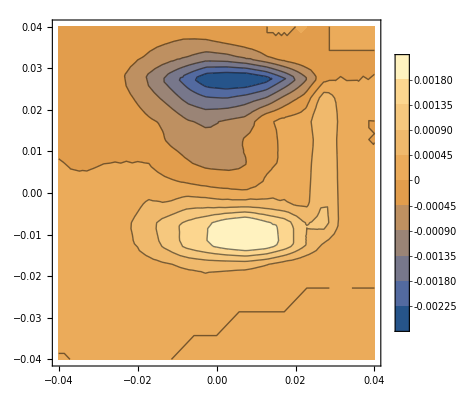

```mathematica
ContourPlot[(InterpolMCData[x,y]-InterpolTransferData[x,y]),{x,-0.04,0.04},{y,-0.04,0.04},PlotRange->All,PlotLegends->Automatic,Contours->10]
```

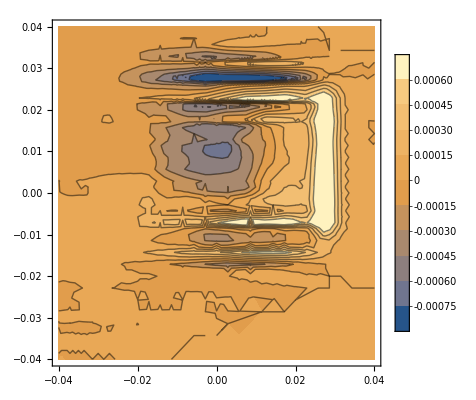

```mathematica
ContourPlot[(InterpolMCData[x,y]-InterpolTransferData[x,y+0.00135]),{x,-0.04,0.04},{y,-0.04,0.04},PlotRange->All,PlotLegends->Automatic,Contours->10]
```

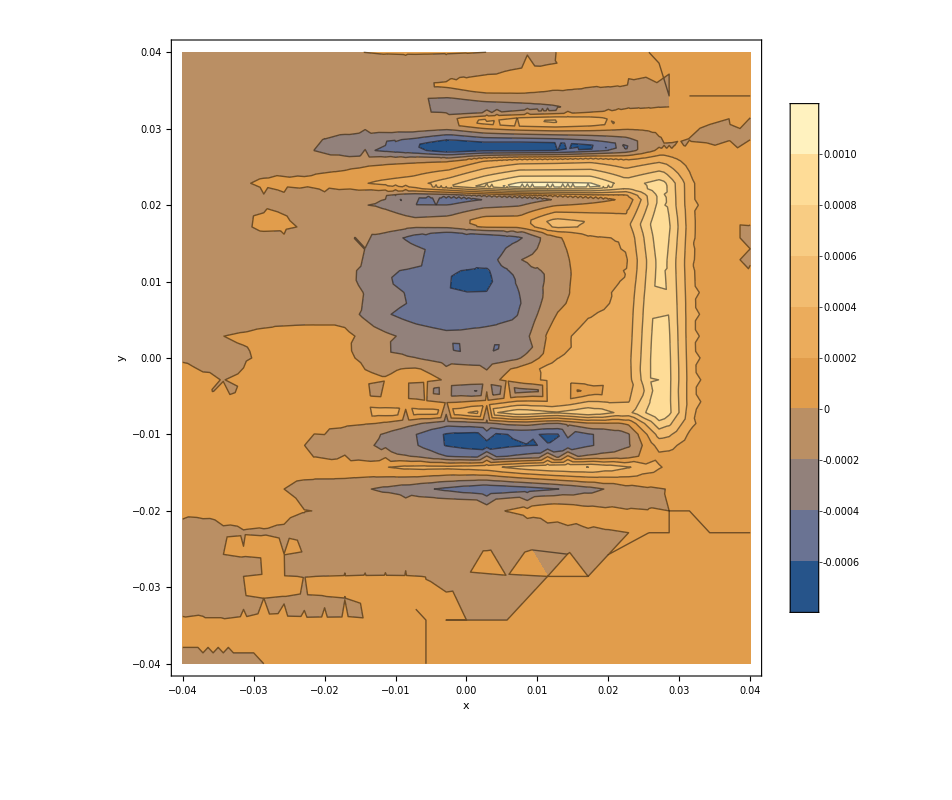

```mathematica
ContourPlot[{
(*(InterpolMCData[x,y]-InterpolTransferData[x,y]),*)
(InterpolMCData[x,y]-InterpolTransferData[x-0.000,y+0.00155])
},{x,-0.04,0.04},{y,-0.04,0.04},PlotRange->All,PlotLegends->Automatic,PlotStyle->Opacity[0.7],FrameLabel->{"x","y"(*,"MC - Transfer"*)},ImageSize->800]
```

### 1D - y

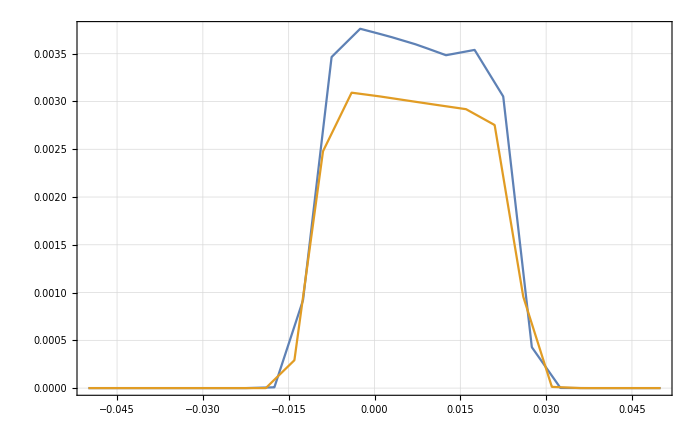

```mathematica
Plot[{InterpolMCData[0.025,y],InterpolTransferData[0.025,y+0.0015]},{y,-0.05,0.05}]
```

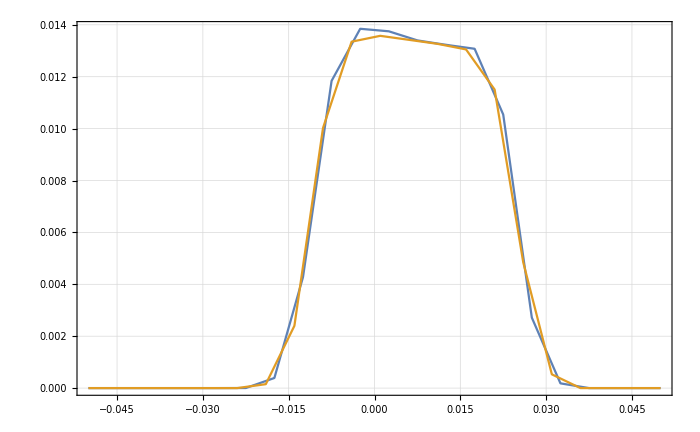

```mathematica
Plot[{InterpolMCData[0.015,y],InterpolTransferData[0.015,y+0.0015]},{y,-0.05,0.05}]
```

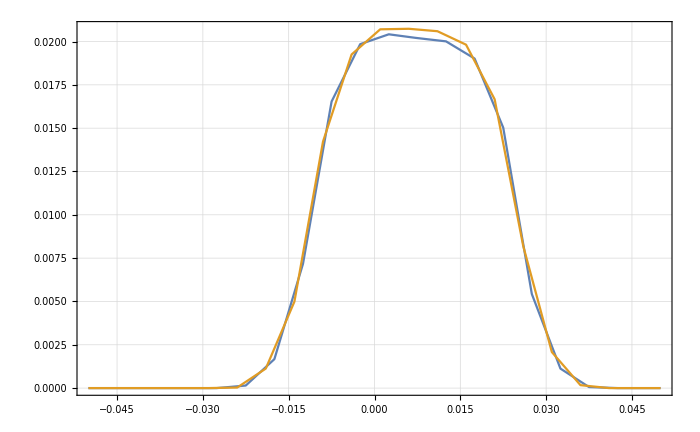

```mathematica
Plot[{InterpolMCData[0.005,y],InterpolTransferData[0.005,y+0.0015]},{y,-0.05,0.05}]
```

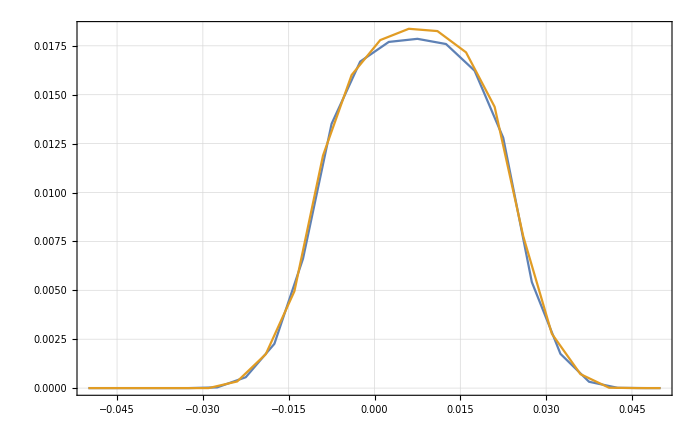

```mathematica
Plot[{InterpolMCData[-0.005,y],InterpolTransferData[-0.005,y+0.0015]},{y,-0.05,0.05}]
```

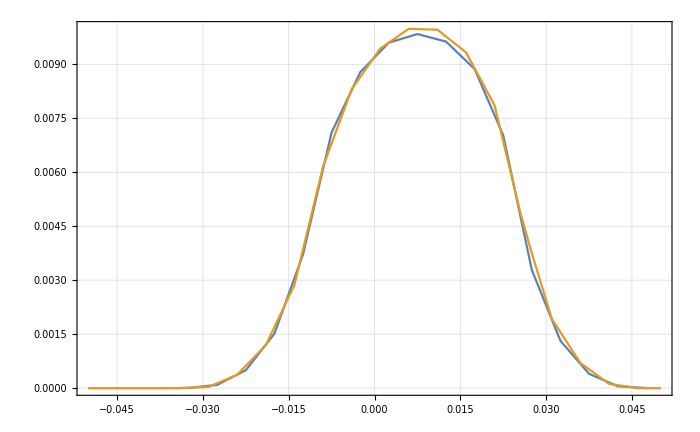

```mathematica
Plot[{InterpolMCData[-0.015,y],InterpolTransferData[-0.015,y+0.0015]},{y,-0.05,0.05}]
```

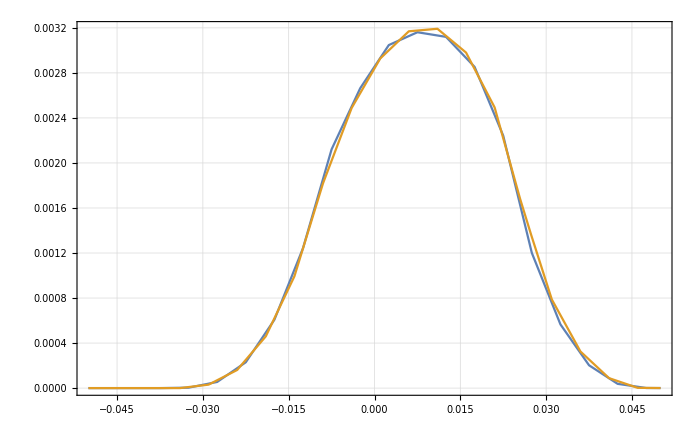

```mathematica
Plot[{InterpolMCData[-0.025,y],InterpolTransferData[-0.025,y+0.0015]},{y,-0.05,0.05}]
```

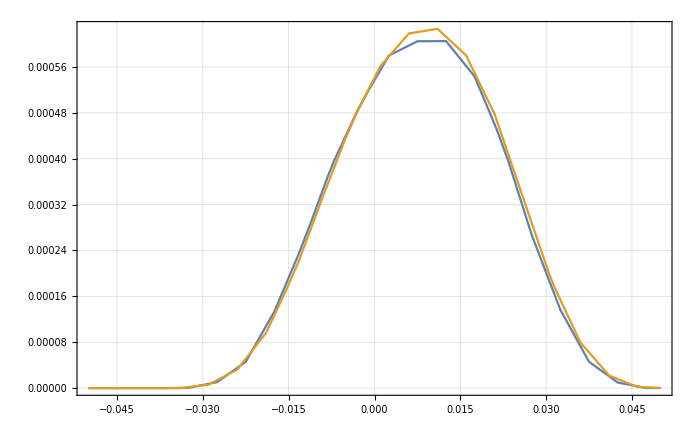

```mathematica
Plot[{InterpolMCData[-0.035,y],InterpolTransferData[-0.035,y+0.0015]},{y,-0.05,0.05}]
```

### in x

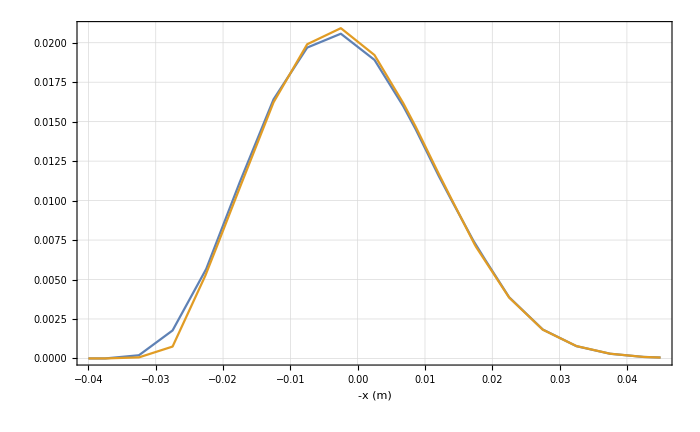

```mathematica
Plot[{InterpolMCData[-x,0],InterpolTransferData[-x,0.0015]},{x,-0.04,0.045},FrameLabel->{"-x (m)",None}]
```

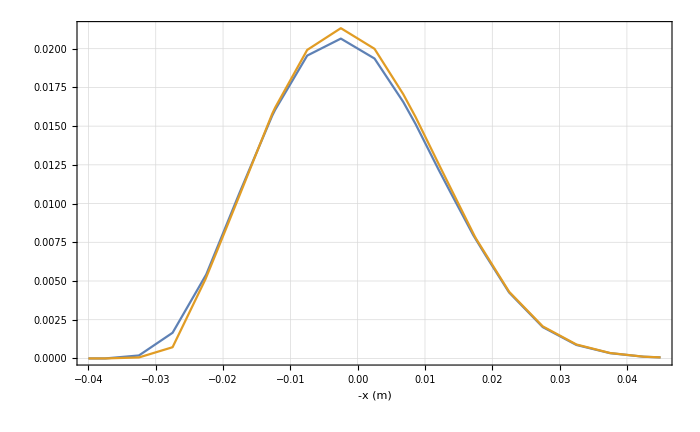

```mathematica
Plot[{InterpolMCData[-x,0.01],InterpolTransferData[-x,0.01+0.0015]},{x,-0.04,0.045},FrameLabel->{"-x (m)",None}]
```

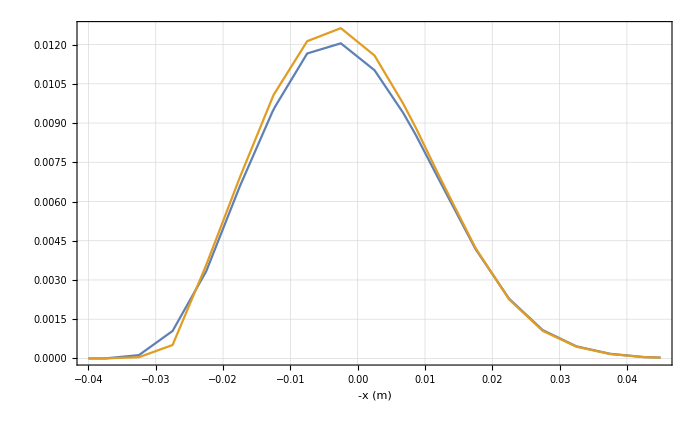

```mathematica
Plot[{InterpolMCData[-x,-0.01],InterpolTransferData[-x,-0.01+0.0015]},{x,-0.04,0.045},FrameLabel->{"-x (m)",None}]
```

# One to One mapping investigations to cross check Transfer compared to tracks

### for now, you have to evaluate this after the other stuff, no dependency built in!

```mathematica
Get["NeutronBeam/OnetoOneMapping.m"]
```

### in track, we use momentum 1187.28, not more digits

```mathematica
pmaxlocal=1187.28*1000;
```

```mathematica
Eofp[pmaxlocal]-me
```

781577.

```mathematica
E0-me
```

781582.

```mathematica
StartPointsTrack={{0.,0.},{-0.005,-0.01749999999999996},{-0.005,0.01750000000000007},{0.005,-0.01749999999999996},{0.005,0.01750000000000007}}
```

{{0.,0.},{-0.005,-0.0175},{-0.005,0.0175},{0.005,-0.0175},{0.005,0.0175}}

```mathematica
DetPointsTrack={{-0.05890494,0.013902999999999999},{-0.06327412,-0.00413959999999991},{-0.06490085,0.03174600000000005},{-0.05291088,-0.003939799999999938},{-0.05453779,0.031943000000000055}}
```

{{-0.0589049,0.013903},{-0.0632741,-0.0041396},{-0.0649009,0.031746},{-0.0529109,-0.0039398},{-0.0545378,0.031943}}

```mathematica
xDofDV[0.,0.,0.,pmaxlocal,0.,AlphaFromBlines,BRxBCenterFromBLines,rRxB,rDet,0.,R,1,1,{YRxBShift,0.,YDetShift}]
```

-0.0578811

```mathematica
xDofDV[0.,0.,0.01,pmaxlocal,0.,AlphaFromBlines,BRxBCenterFromBLines,rRxB,rDet,0.,R,1,1,{YRxBShift,0.,YDetShift}]
```

-0.0475986

```mathematica
-xDofDV[0.,0.,-0.01,pmaxlocal,0.,AlphaFromBlines,BRxBCenterFromBLines,rRxB,rDet,0.,R,1,1,{YRxBShift,0.,YDetShift}]
```

0.0681635

### for the x transfer, we have to invert the xDV as well as the xDet, because drift distance the other way around

```mathematica
TransferDetPoints={xDofDV[0.,#[[2]],#[[1]],pmaxlocal,0.,AlphaFromBlines,BRxBCenterFromBLines,rRxB,rDet,0.,R,1,1,{YRxBShift,0.,YDetShift}],yDofDV[0.,#[[2]],pmaxlocal,0.,BRxBCenterFromBLines,rRxB,rDet,0.,YDetShift]}&/@StartPointsTrack
```

{{-0.0578811,0.015928},{-0.0620126,-0.00206629},{-0.0640313,0.0339223},{-0.0517301,-0.00206629},{-0.0537488,0.0339223}}

```mathematica
TransferDetPoints-DetPointsTrack
```

{{0.00102386,0.002025},{0.00126152,0.00207331},{0.00086958,0.00217629},{0.00118073,0.00187351},{0.000788974,0.00197929}}

```mathematica
{{0.0010238612165434022,0.0020250000000001656},{0.0012615210982050776,0.0020733059741986615},{0.0008695797946050993,0.002176294025801634},{0.001180734827234478,0.0018735059741986893},{0.0007889735236345022,0.001979294025801631}}[[All,2]]//Mean
```

0.00202548

### for y, difference to track is roughly 2 mm

### for x, difference is roughly 1 mm

### what difference would the non-adiabtic angle in RxB do

```mathematica
D1stBPolyGrad[pmaxlocal,AlphaFromBlines,0.,BRxBCenterFromBLines,rRxB,0.,R,1,1]
```

0.0561003

```mathematica
D1stBPolyGrad[pmaxlocal,AlphaFromBlines,1/180*Pi,BRxBCenterFromBLines,rRxB,0.,R,1,1]
```

0.0561003

```mathematica
D1stBPolyGrad[pmaxlocal,AlphaFromBlines,1/180*Pi,BRxBCenterFromBLines,rRxB,0.,R,1,1]-D1stBPolyGrad[pmaxlocal,AlphaFromBlines,0.,BRxBCenterFromBLines,rRxB,0.,R,1,1]
```

6.43857×10^-10

### so this cant be it

# Cross check if new sign of drift gives correct result

## mit altem drift vorzeichen

```mathematica
ApertXOff
```

0.0301277

```mathematica
ManualphiAIntegrandAllLimitsShift[0.,0.,0.03,{0.,0.,900000,Pi/4},{Pi,BRxB,rRxB,rA,rDet,R,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,-ApertXOff,ApertYOff}]
```

0.00017437

### hier theta = 0

```mathematica
DeltaxDV2Shift[0.,0.,0.03,900000,0,Pi,BRxB,rRxB,rDet,0.,R,1,1,{0,0,0}]
```

-0.0136334

```mathematica
pLimitsApertXListShift[0.,0.03,Pi/4,Pi,BRxB,rRxB,rA,rDet,0.,R,1,1,-ApertXOff,ApertX,{0,0,0,0}]
```

{752373.,890732.,1.07021×10^6,1.18728×10^6}

## mit neuem Vorzeichen

```mathematica
ManualphiAIntegrandAllLimitsShift[0.,0.,0.03,{0.,0.,900000,Pi/4},{Pi,BRxB,rRxB,rA,rDet,R,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,-ApertXOff,ApertYOff}]
```

0.

```mathematica
DeltaxDV2Shift[0.,0.,0.03,900000,0,Pi,BRxB,rRxB,rDet,0.,R,1,1,{0,0,0}]
```

0.0719853

```mathematica
pLimitsApertXListShift[0.,0.03,Pi/4,Pi,BRxB,rRxB,rA,rDet,0.,R,1,1,-ApertXOff,ApertX,{0,0,0,0}]
```

{0,1.18728×10^6}

### mit neuem Vorzeichen, invertierte startwerte

```mathematica
ManualphiAIntegrandAllLimitsShift[0.,0.,0.03,{0.,0.,900000,Pi/4},{Pi,BRxB,rRxB,rA,rDet,R,1,1},{0,0,0,0,0},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff}]
```

0.

```mathematica
ApertXOff
```

0.0301277

```mathematica
DeltaxDV2Shift[0.,0.,-0.03,900000,0,Pi,BRxB,rRxB,rDet,0.,R,1,1,{0,0,0}]
```

0.0136334

```mathematica
pLimitsApertXListShift[0.,-0.03,0.,Pi,BRxB,rRxB,rA,rDet,0.,R,1,1,ApertXOff,ApertX,{0,0,0,0}]
```

{1.1403×10^6,1.18728×10^6}

### so for th=0, it works. but as soon as th not 0, phase will add rG differently, scales differently with ratios, so results might be different

# Vary b for manual fit of spectrum

```mathematica
{XAShift,YAShift,YRxBShift,XDetShift,YDetShift}
```

{0.,0.00718805,0.00677285,0.,0.015928}

```mathematica
{ApertX,ApertY,ApertXOff,ApertYOff}
```

{0.01,0.035,0.03,0.}

```mathematica
CloseKernels[]
LaunchKernels[3]
```

{}

{KernelObject[1,local],KernelObject[2,local],KernelObject[3,local]}

```mathematica
{{a,b},{ce,d}}-{{0.,0.},{0.002,0.002}}
```

{{0.+a,0.+b},{-0.002+ce,-0.002+d}}

```mathematica
CenterfitG1=0.96907;
CenterfitG2=0.973888;
```

```mathematica
BfromCenter=0.221032;
```

```mathematica
BinwYShiftPrec44OriginalBinsb0NewBGrad=ParallelMap[AbsoluteTiming[BinIntShift[0.0,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BfromCenter,rF,rRxB,rA,rDet,R,CenterfitG1,CenterfitG2},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesOriginal[[1;;2]],Method->"FinestGrained"]
```

{{10.7967,0.},{10.7965,0.}}

```mathematica
E0-me
```

781582.

### b=0.5E-3

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb0005Part1=ParallelMap[AbsoluteTiming[BinIntShift[0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal[[1;;180]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0005Part1={{11.377193,0.},{11.456761,0.},{11.536587,0.},{11.726905,0.},{11.989198,0.},{12.295547,0.},{13.000371,0.},{12.663374,0.},{12.644672,0.},{12.884005,0.},{13.175668,0.},{13.222444,0.},{12.831003,0.},{12.471598,0.},{12.122052,0.},{12.730308,0.},{12.582633,0.},{12.946794,0.},{14.896147,0.},{15.281336,0.},{15.352612,0.},{12.624058,0.},{12.107313,0.},{12.148997,0.},{12.43258,0.},{12.79049,1.0405048941437933*^-13},{12.851294,7.708448815063789*^-11},{12.898133,3.271245323773834*^-10},{13.456432,2.592402903640472*^-10},{12.70736,6.267620983457833*^-11},{12.71348,6.5240123128758045*^-12},{12.633559,8.648185719564161*^-14},{12.824922,0.},{13.14936,0.},{12.8901,0.},{12.36568,0.},{12.391798,0.},{12.082629,0.},{12.274892,0.},{12.203259,0.},{12.211899,0.},{12.25059,0.},{12.227208,0.},{12.014422,0.},{12.396396,0.},{12.873519,0.},{12.787725,1.5506158739354946*^-11},{61.207802,1.733314209052099*^-8},{198.470833,1.1234414381017693*^-7},{242.861578,2.577848660132963*^-7},{256.301888,3.3980732910771667*^-7},{286.506406,3.1493523019129476*^-7},{238.009847,2.497531498162689*^-7},{227.06182,1.908041786270378*^-7},{201.171244,1.4265380293788803*^-7},{174.010443,9.641408206795245*^-8},{144.895703,4.617110280911362*^-8},{59.428781,1.2897834363202254*^-8},{22.484178,2.95164235280223*^-10},{12.376302,0.},{12.233298,0.},{12.267682,0.},{12.135061,0.},{12.199583,0.},{12.220603,0.},{12.089484,0.},{13.30186,0.},{13.151055,0.},{66.362592,7.02296321787859*^-8},{353.842817,9.540060102363034*^-7},{563.044271,3.030928699486376*^-6},{641.65218,5.811842943299369*^-6},{640.02773,7.941237788601574*^-6},{631.124648,8.513800039964891*^-6},{685.883286,7.838885239349377*^-6},{667.051178,6.7954415407790625*^-6},{663.482836,5.677512957157973*^-6},{611.495667,4.207520419135217*^-6},{540.289982,2.4550344450229102*^-6},{376.347637,9.638825806762386*^-7},{164.331521,1.785618112749869*^-7},{15.463799,5.927471694602762*^-10},{12.056726,0.},{12.52544,0.},{12.321671,0.},{12.336522,0.},{12.354168,0.},{12.345468,0.},{14.808483,0.},{44.314009,1.5477583784790687*^-7},{230.423404,2.2753529880789003*^-6},{683.957788,9.598041014255208*^-6},{1260.241532,0.00002433597324084374},{1377.036652,0.000042863102921960925},{1505.575828,0.00005841578709243564},{1809.908603,0.00006582426452805976},{1772.903837,0.00006500659425919821},{1477.391702,0.000059572612538752405},{1528.254446,0.00005123110103838601},{1560.038682,0.00003922912093556228},{1277.682256,0.000024842179010705494},{859.326357,0.000011905199512119659},{487.735033,3.6716629710498923*^-6},{128.636272,4.793164024505979*^-7},{13.884201,9.28010227986257*^-11},{13.506724,0.},{13.424778,0.},{14.340281,0.},{14.157699,0.},{13.162525,0.},{15.836795,0.},{156.641665,2.221134570869961*^-6},{404.475537,0.000014153334599083864},{996.064624,0.00004737845610021373},{1730.122642,0.00010788443386420498},{2259.658054,0.00018160441621989417},{2734.746933,0.000246442482966504},{2708.0934,0.00028425050606339437},{3041.558942,0.00029134548776520955},{2707.126975,0.0002744772651273121},{2994.342439,0.00023907468113393518},{2753.602852,0.0001866595675294305},{2385.596566,0.00012395203870541253},{1605.295846,0.00006554321640652128},{965.288968,0.000024846304725472085},{279.382018,6.243645258103563*^-6},{78.986542,5.871673503144523*^-7},{14.857625,0.},{14.83113,0.},{14.803858,0.},{14.849639,0.},{14.785868,0.},{18.608986,0.},{439.883044,6.957194285839705*^-6},{829.168754,0.00004933613414579537},{1049.514224,0.0001573155774961678},{1993.39239,0.00033764594018001297},{2493.819314,0.0005581737483389413},{2642.605708,0.0007569738637401442},{3555.202635,0.0008824876374429562},{3614.99876,0.0009216576066217255},{3103.738087,0.000881761658627134},{2846.313342,0.0007746743165763398},{2748.037842,0.0006129537350714986},{2474.512556,0.00041825270414622677},{1823.752795,0.0002332142220574445},{1084.569574,0.00009822389638127518},{559.89818,0.00002738473490023963},{265.020677,3.4947175305521524*^-6},{15.659785,0.},{15.757389,0.},{15.592159,0.},{15.671709,0.},{15.56487,0.},{25.050966,0.},{590.90072,0.000020100449706159942},{1038.837862,0.00013050117099053555},{1480.222774,0.0003976726420692535},{2289.254309,0.00084504098834497},{3231.854429,0.0014167222784869518},{3253.695578,0.001933508335548589},{3194.104037,0.0022561041439872957},{3864.249784,0.002372136342185955},{3457.674317,0.002287550182497969},{3533.162772,0.0020256399146061158},{3066.844307,0.001619699555481917},{3245.889528,0.001116867028759111},{1833.040405,0.0006328159635038571},{1398.183187,0.0002789500967375878},{944.906231,0.00008353035575527547},{541.224724,0.000011079286253521068},{18.931143,0.},{18.676913,0.},{18.30268,0.},{18.007939,0.},{17.785376,0.},{27.947621,0.},{672.44907,0.00003606204808754952},{1266.885505,0.00027167044015101417},{1991.900736,0.0008265245076795986}};
```

#### took 42951 for 3 cores

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb0005Part2=ParallelMap[AbsoluteTiming[BinIntShift[0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal[[181;;-1]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0005Part2={{2147.540936,0.0017982098084307328},{3493.071344,0.003236004728948514},{4518.108221,0.004498215903949417},{4396.914552,0.0052027068836282536},{5449.645786,0.00545172501186099},{4802.487202,0.005278376946311744},{3431.512859,0.004719413630154708},{3439.088914,0.003823588728341946},{2791.551113,0.002614800829516656},{2055.785053,0.001427734484039614},{1858.221874,0.0006325987017455385},{1619.326537,0.00019628818493131882},{774.81083,0.00002604038151121469},{28.680831,0.},{27.705829,0.},{25.61601,0.},{26.640058,0.},{26.347903,0.},{33.192231,0.},{662.607601,0.000035054863354438566},{2144.193624,0.00045986985907759347},{2389.156442,0.001457219515432863},{3400.36025,0.003324215759366873},{3520.590638,0.006643953564479918},{5741.48693,0.009487890752446047},{6151.656237,0.010853776786550886},{6382.691984,0.011335840511204722},{6642.345184,0.011036508243837617},{5047.507298,0.010012704483616535},{4421.292406,0.008281776025778877},{3132.706871,0.005559951784155979},{3088.907627,0.002775370212579812},{2320.431102,0.0011922882651299194},{1739.326122,0.00036599263399030805},{788.977791,0.000045831145827160665},{28.086392,0.},{27.77477,0.},{27.572615,0.},{27.370707,0.},{27.284492,0.},{33.095581,0.},{214.161869,2.020665860031028*^-6},{1995.883648,0.0006300917694849323},{2857.020686,0.00221648530253199},{3551.346307,0.0053666532549227885},{5098.369942,0.011780545249719774},{6408.678995,0.017238783587043505},{4636.46247,0.019629003642741602},{6557.316909,0.020509809188239116},{6954.666233,0.02011644373495891},{4753.209625,0.018524946358530935},{6097.389742,0.015644658889990393},{4610.965645,0.010331969900632062},{3547.163763,0.004703769731397715},{2724.606581,0.0019237834570564039},{1983.767356,0.0005544422983244825},{255.269328,0.000023045534069326294},{32.147878,0.},{31.909103,0.},{31.759227,0.},{31.556185,0.},{31.492006,0.},{33.226503,0.},{33.22783,0.},{1499.281748,0.0005693698872371448},{3544.552699,0.002908831381334318},{3357.050594,0.0076022156914740905},{5141.311343,0.01799100053887509},{6411.989532,0.026820129962121235},{6884.518129,0.03054285385943712},{6977.311342,0.031963148659525126},{7526.220238,0.031558579367211764},{6865.253737,0.029430444263048423},{6415.957556,0.02520697225269865},{5493.581468,0.016473844605225444},{3708.37868,0.006967663029244836},{3491.670098,0.00267146481060419},{2077.917254,0.0006378126471336704},{32.835538,0.},{32.858699,0.},{32.964442,0.},{32.860412,0.},{32.857189,0.},{32.852578,0.},{33.149402,0.},{33.184095,0.},{1097.279221,0.00041707329032284845},{3767.675813,0.003225404100069967},{4282.816099,0.00950271262337461},{5208.740937,0.024089678864843957},{8178.338737,0.03655520866658166},{8415.143298,0.04167449171461947},{6549.542544,0.04355790172029162},{6203.232251,0.04325642529784671},{7309.295673,0.040827160247926333},{7474.035914,0.03532302368003969},{5499.56267,0.02285589656389696},{4179.077601,0.009035216014560421},{3766.392355,0.003145276483200492},{1561.47064,0.0005302461080458263},{33.687787,0.},{33.944955,0.},{33.711388,0.},{39.47151,0.},{38.3681,0.},{39.944796,0.},{36.990068,0.},{40.041693,0.},{548.034215,0.00012442397198120356},{3097.168227,0.002871992587212757},{4333.805655,0.010339414124219827},{5878.778578,0.028629613317288572},{7854.556807,0.044350245054738766},{7279.852929,0.05055183153641125},{4605.508119,0.052479977747658405},{4867.487679,0.052409044280349565},{7252.351669,0.05023584814228352},{7538.893063,0.043815509577555395},{6143.463687,0.02800006477460354},{4264.569725,0.010230775893313634},{3234.053543,0.0030334919828498242},{445.9793,0.00014792283643823263},{32.783036,0.},{32.787031,0.},{32.785227,0.},{32.890158,0.},{32.897414,0.},{32.91815,0.},{31.989051,0.},{32.010491,0.},{32.062037,0.},{1769.443887,0.0017742720031888233},{4122.648401,0.00961386207132323},{4897.819314,0.0302545933933584},{6425.105335,0.04801184019982231},{5268.466168,0.054430585059636556},{3095.660657,0.055871118493462865},{3635.304354,0.05608206305754788},{5880.50606,0.05483432626212627},{6712.054751,0.048400597014060534},{6064.221824,0.030389389173312086},{4007.17805,0.009901977307073444},{2478.534929,0.0020976622260903475},{32.18833,0.},{32.203037,0.},{32.147883,0.},{32.178967,0.},{32.265172,0.},{32.342152,0.},{32.403331,0.},{31.730835,0.},{31.731047,0.},{31.732285,0.},{959.254905,0.0006909105241606742},{3194.182489,0.007361187374070082},{5086.105985,0.02822857273499851},{5759.997447,0.046033722610654734},{3681.478348,0.051322413230471056},{2216.068882,0.052157523184046935},{1902.610418,0.05254085937672819},{3834.502598,0.052372796369332515},{5354.089117,0.047239813699947696},{4901.418904,0.028945144647480388},{3551.872895,0.007853659732864478},{1094.231085,0.0009752725487178548},{31.552258,0.},{31.563258,0.},{31.561024,0.},{31.514024,0.},{31.681541,0.},{31.664785,0.},{31.678725,0.},{31.561801,0.},{31.625448,0.},{31.586888,0.},{435.309543,0.0001209169540131955},{2472.779719,0.004328389649474213},{4798.032876,0.022799959630991348},{5381.448305,0.03823156012459773},{2732.269273,0.041399544526102006},{1907.801576,0.041914419935314494},{1949.936433,0.04236598740050765},{2877.013429,0.04271025091992218},{4993.545044,0.03986443533962853},{4852.927894,0.023764883625697623},{2486.634226,0.004768437715125429},{376.656198,0.0001563346725298895},{31.46758,0.},{31.471434,0.},{31.539748,0.},{31.498945,0.},{31.463462,0.},{31.480681,0.},{31.452421,0.},{31.465782,0.},{31.481556,0.},{31.492374,0.},{31.469524,0.},{1474.249235,0.0017299444042347765},{3669.165497,0.015263510061412345},{3290.109636,0.026101725399932177},{1242.938513,0.02737779966646313},{1134.796042,0.027733173379140053},{1140.435891,0.028093294166066225},{1203.627253,0.02845503392410991},{3448.551638,0.02761659193086401},{4407.17378,0.01610866906020391},{1635.853539,0.0019477520380520223},{31.634145,0.},{31.637759,0.},{31.637917,0.},{31.605958,0.},{31.606855,0.},{31.610865,0.},{31.610352,0.},{31.584276,0.},{31.882554,0.},{31.814504,0.},{31.860531,0.},{31.810719,0.},{1038.756428,0.00039983139914043036},{3336.680074,0.00765957958761387},{2298.305614,0.013140664329398446},{1054.566961,0.01347826386149027},{1058.40342,0.013672701574706927},{1061.951364,0.013870903349435266},{1062.889779,0.014072911922612737},{2216.403992,0.014064106882395642},{3523.173046,0.008147531514673335},{1092.767664,0.0004563751123686549},{31.259189,0.},{31.261474,0.},{31.247701,0.},{31.263819,0.},{31.271951,0.},{31.24252,0.},{31.232644,0.},{31.254679,0.},{22.943615,0.},{22.961991,0.},{23.039905,0.},{23.286533,0.},{435.419829,0.00002456737268526482},{2432.015432,0.0010868578629235947},{1943.209967,0.001825792498588399},{1734.993386,0.0018635246252644668},{1743.643637,0.0018979082816862514},{1775.069255,0.0019331285916726647},{1779.825179,0.001969204932673073},{2194.618346,0.001998080101527941},{2743.480846,0.0011809438043774323},{378.038246,0.000028071857674262967},{23.280357,0.},{23.019766,0.},{22.99061,0.},{22.948856,0.},{22.943276,0.},{22.973648,0.},{22.947197,0.},{22.865555,0.},{21.313941,0.},{21.293332,0.},{21.385725,0.},{21.626217,0.},{22.28535,0.},{852.177407,0.00009496881627125221},{790.766488,0.00016022551177279618},{863.730287,0.00016345952697718343},{867.580827,0.00016677920022136904},{908.441954,0.0001701866112188807},{928.388856,0.0001736847492115331},{938.343113,0.00017727603936511235},{1102.920765,0.00010500652076335863},{22.191057,0.},{21.601773,0.},{21.470745,0.},{21.39172,0.},{21.281372,0.},{21.248702,0.},{21.270084,0.},{21.207768,0.},{21.217477,0.},{16.088925,0.},{16.129581,0.},{16.208802,0.},{16.435844,0.},{16.962694,0.},{29.882939,1.291149645343689*^-7},{35.779723,1.5547173020114256*^-7},{35.550487,1.5825983241884981*^-7},{35.237057,1.611174089299902*^-7},{35.340055,1.6404625951989058*^-7},{35.744758,1.670482375126902*^-7},{39.007542,1.7011350495791097*^-7},{36.006197,1.4599157940930208*^-7},{17.088644,0.},{16.527924,0.},{16.291173,0.},{16.219104,0.},{16.184204,0.},{16.185288,0.},{16.190748,0.},{16.182071,0.},{16.189012,0.},{14.193742,0.},{14.231914,0.},{14.329092,0.},{14.535282,0.},{15.124636,0.},{16.004067,0.},{16.005966,0.},{15.711925,0.},{15.658531,0.},{15.625025,0.},{15.760116,0.},{15.943834,0.},{16.082523,0.},{15.06325,0.},{14.550241,0.},{14.26499,0.},{14.250067,0.},{14.169519,0.},{14.217195,0.},{14.190621,0.},{14.226455,0.},{13.781093,0.}};
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0005=Join[BinYShiftwShiftPrec44OriginalBinsb0005Part1,BinYShiftwShiftPrec44OriginalBinsb0005Part2];
```

```mathematica
Length[BinYShiftwShiftPrec44OriginalBinsb0005]
```

506

### b= - 0.5E-3

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm0005Part1=ParallelMap[AbsoluteTiming[BinIntShift[-0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal[[1;;180]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005Part1={{11.49561,0.},{11.534876,0.},{11.67418,0.},{11.681194,0.},{11.865513,0.},{12.27658,0.},{12.208783,0.},{12.056112,0.},{12.020637,0.},{12.076423,0.},{12.125783,0.},{12.310834,0.},{12.424404,0.},{12.02897,0.},{11.876845,0.},{11.772327,0.},{11.77069,0.},{11.84452,0.},{11.883804,0.},{12.020783,0.},{11.991261,0.},{12.043779,0.},{11.616593,0.},{11.563839,0.},{11.679025,0.},{11.911594,1.0407748892827994*^-13},{12.303002,7.710436805980266*^-11},{12.436466,3.272088740247634*^-10},{12.636864,2.5930720673836665*^-10},{12.304055,6.269242602263214*^-11},{12.181613,6.52570439942571*^-12},{12.118652,8.650433345472686*^-14},{12.149661,0.},{12.346308,0.},{12.370438,0.},{11.920022,0.},{11.702565,0.},{11.510268,0.},{11.480536,0.},{11.551934,0.},{11.528772,0.},{11.571624,0.},{11.6392,0.},{11.599383,0.},{11.867556,0.},{11.943093,0.},{12.163257,1.5510139284516448*^-11},{59.330007,1.733749499675003*^-8},{191.911828,1.1237214324276462*^-7},{233.903379,2.5784889045824656*^-7},{245.70398,3.398917432721505*^-7},{265.648017,3.1501365633692555*^-7},{216.082709,2.498154770297241*^-7},{209.714183,1.908518912708202*^-7},{200.230877,1.4268953496602815*^-7},{173.783645,9.643826949960647*^-8},{144.808487,4.618271450242523*^-8},{66.159393,1.2306093764632308*^-8},{22.490532,2.9523973821157874*^-10},{12.379987,0.},{12.231447,0.},{12.274585,0.},{12.151723,0.},{12.204836,0.},{12.219536,0.},{12.151563,0.},{13.304981,0.},{13.187831,0.},{66.73724,7.024687684773582*^-8},{353.24531,9.542377941127231*^-7},{563.873041,3.031657087875256*^-6},{645.227571,5.813232741777251*^-6},{627.894716,7.943136926338247*^-6},{609.274085,8.515841636385382*^-6},{631.035459,7.840770605951806*^-6},{577.678621,6.797079595946495*^-6},{568.519507,5.678883223507027*^-6},{550.54362,4.2085370213810225*^-6},{521.516525,2.4556293749915582*^-6},{368.265724,9.641178832425*^-7},{161.525607,1.7860597255325207*^-7},{15.323109,5.928981993492391*^-10},{11.918746,0.},{11.984695,0.},{12.043598,0.},{12.171601,0.},{12.259004,0.},{12.271546,0.},{14.708805,0.},{43.863719,1.5481345991166712*^-7},{229.419821,2.2758968701931984*^-6},{667.111144,9.600286984949088*^-6},{1223.65526,0.0000243415882626938},{1336.714404,0.00004287292324897505},{1477.066964,0.00005842915699739857},{1787.407722,0.0000658393736584711},{1742.918583,0.00006502157357258954},{1447.377461,0.000059586373141923456},{1486.269865,0.000051242944642801144},{1516.596563,0.000039238200317679077},{1244.240462,0.00002484796099567325},{838.661452,0.000011908007923057462},{475.785519,3.6725373407972345*^-6},{127.338155,4.794327912888597*^-7},{13.694055,9.282490174313972*^-11},{13.360596,0.},{13.220814,0.},{13.194918,0.},{13.076224,0.},{12.92793,0.},{15.534069,0.},{153.133153,2.2216593924413176*^-6},{371.963879,0.000014156600068592951},{919.540167,0.00004738907788939066},{1634.046174,0.00010790817976139027},{2198.524555,0.00018164401924185768},{2708.567878,0.00024649611328822816},{2698.034911,0.00028431254088822413},{3038.494277,0.00029140936485709843},{2705.86521,0.0002745376060118695},{2988.616005,0.00023912726105106589},{2748.806121,0.00018670067677208947},{2384.001066,0.00012397948656604885},{1604.378455,0.0000655579024483908},{961.097131,0.000024851981382591074},{278.373929,6.245110157401562*^-6},{78.519699,5.873084575007918*^-7},{14.839007,0.},{14.798869,0.},{14.769674,0.},{14.790631,0.},{14.75527,0.},{18.590013,0.},{438.744794,6.9587986652060745*^-6},{831.872156,0.000049347022224573615},{1047.500556,0.00015734910384378626},{1985.86641,0.00033771631750662397},{2501.252271,0.0005582887919695472},{2637.643143,0.0007571294157538847},{3545.279882,0.0008826694518770241},{3622.353286,0.0009218484183924022},{3105.749032,0.0008819447274792027},{2834.108086,0.0007748351773268335},{2746.469064,0.0006130812386115791},{2474.861757,0.0004183402882544468},{1819.874796,0.00023326377532767169},{1084.579044,0.00009824527875188773},{559.654768,0.000027390913532813917},{264.564236,3.495536041485998*^-6},{15.637256,0.},{15.592969,0.},{15.5703,0.},{15.514851,0.},{15.599295,0.},{24.846677,0.},{592.889692,0.000020104911116501977},{1034.332457,0.0001305285513538111},{1474.059059,0.0003977525767244936},{2292.754401,0.000845206622697025},{3226.709699,0.0014169968762089728},{3238.014019,0.0019338818762773718},{3200.973683,0.0022565405885595687},{3872.450903,0.0023725973187389794},{3438.700397,0.0022879958794438083},{3535.190924,0.0020260346370555063},{3071.974087,0.0016200158891380356},{3235.333359,0.0011170867523675524},{1836.430444,0.000632942474756034},{1395.979336,0.0002790074838298688},{946.729339,0.00008354830364759366},{539.378176,0.000011081797105206857},{18.922962,0.},{18.625221,0.},{18.268179,0.},{17.987342,0.},{17.757101,0.},{27.93559,0.},{672.275098,0.00003606969962155444},{1263.533099,0.00027172425303038396},{1978.446404,0.000826680588275604}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm0005Part2=ParallelMap[AbsoluteTiming[BinIntShift[-0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal[[181;;254]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005Part2={{2104.884523,0.0017985370962613698},{3428.215988,0.0032365936962899353},{4409.965672,0.004499033637622755},{4286.686152,0.005203651486070573},{5697.219249,0.005452722712341118},{4758.917872,0.005279340197478913},{3421.368731,0.004720275656525673},{3378.324045,0.003824289827532185},{2741.45519,0.0026152828463594877},{2011.442116,0.00142800020273207},{1744.147925,0.00063272050771822},{1526.030354,0.00019633264319465193},{726.882365,0.00002604603634274746},{25.185783,0.},{24.869668,0.},{24.578494,0.},{24.431383,0.},{24.053906,0.},{32.087323,0.},{629.914246,0.000035061873293398596},{2016.692965,0.00045995498779142845},{2262.495633,0.001457470399056904},{3225.795853,0.0033247672686882454},{3402.750186,0.006645069618339188},{5537.416358,0.009489486741038635},{5912.004242,0.010855597302533018},{6189.416097,0.01133774791880265},{6552.657176,0.01103837127340885},{5024.192455,0.010014398954735642},{4433.902899,0.008283188120088693},{3138.422055,0.005560902745050819},{3071.439956,0.002775843346046161},{2319.128177,0.0011925000337783401},{1742.262618,0.00036606241723038675},{784.743779,0.000045840692699542266},{27.989993,0.},{27.698424,0.},{27.460106,0.},{27.25683,0.},{27.162791,0.},{32.975413,0.},{213.243396,2.021054804351294*^-6},{1992.379467,0.0006301993735214196},{2860.990425,0.00221682747469292},{3556.028022,0.005367429696725563},{5084.966955,0.011782289890025095},{6416.105965,0.017241342410508554},{4641.739571,0.01963191301943218},{6738.846526,0.02051285255387581},{6945.063854,0.020119459975375262},{4760.012924,0.018527734450005995},{6075.611189,0.015647039013393295},{4620.524025,0.010333548840552343},{3534.239355,0.004704483718307996},{2728.536603,0.0019240922469880525},{1977.525464,0.000554540347754718},{254.447562,0.000023050076071563797},{32.069517,0.},{31.756168,0.},{31.665383,0.},{31.432149,0.},{31.359541,0.},{33.139106,0.},{33.149954,0.},{1496.256193,0.0005694558706996766},{3545.618605,0.0029092200982187575},{3353.15567,0.007603146822722962},{5131.778867,0.017993185614233367},{6393.126872,0.02682338640549837},{6901.241937,0.030546575506266684},{6963.699123,0.03196709257177525},{7514.954897,0.03156250361951363},{6865.969307,0.029434115934716877},{6336.012843,0.025210155426859743}};
```

#### continuation b= - 0.5E-3 (from Daniel PC)

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm0005Part3=ParallelMap[AbsoluteTiming[BinIntShift[-0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesOriginal[[255;;300]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005Part3={{4486.81,0.0164759},{3088.37,0.00696856},{2640.56,0.00267184},{1536.75,0.000637915},{23.9161,0.},{23.8814,0.},{23.9504,0.},{23.9236,0.},{23.9122,0.},{23.872,0.},{24.0534,0.},{24.0086,0.},{807.9,0.000417128},{2780.08,0.00322575},{3160.87,0.0095036},{3947.28,0.0240918},{8147.31,0.0365584},{6559.03,0.0416782},{5203.3,0.0435619},{4822.12,0.0432604},{5771.52,0.0408309},{5900.41,0.0353263},{4296.01,0.0228581},{3228.56,0.00903613},{2885.41,0.00314564},{1182.06,0.000530321},{25.9742,0.},{25.9889,0.},{26.0302,0.},{26.0353,0.},{26.0671,0.},{26.0207,0.},{25.88,0.},{25.636,0.},{405.582,0.000124437},{2390.91,0.00287221},{3378.44,0.01034},{4664.67,0.028631},{5502.32,0.0443523},{7387.07,0.0505543},{4871.55,0.0524827},{4462.18,0.0524118},{5554.53,0.0502385},{5766.71,0.0438178},{5091.76,0.0280016},{3170.15,0.0102315}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm0005Part31=ParallelMap[AbsoluteTiming[BinIntShift[-0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},
{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}
]]&,XYBinBoundariesOriginal[[301;;399]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005Part31={{3483.387051,0.003033758774856185},{454.86163,0.0001479402146590737},{34.37965,0.},{32.999512,0.},{33.313895,0.},{32.892757,0.},{32.889868,0.},{32.899162,0.},{31.921961,0.},{31.984623,0.},{32.025905,0.},{1896.883986,0.001774336751372807},{4654.509186,0.009613991774438403},{5484.450485,0.030254549454006442},{7177.685657,0.048011713550577075},{5767.562607,0.05443062596787319},{3400.429673,0.055871299318493606},{3975.071709,0.056082328688445614},{6288.62799,0.054834597512468095},{7139.959667,0.04840081240204352},{6157.57506,0.030389629695306696},{4028.745368,0.009902222707988906},{2511.919879,0.002097769687606207},{32.536182,0.},{32.206006,0.},{32.325373,0.},{32.301933,0.},{32.385294,0.},{32.38393,0.},{32.461747,0.},{32.139287,0.},{32.136791,0.},{31.847525,0.},{963.823748,0.0006909043945867372},{3206.689444,0.007360897132769396},{5115.7845,0.028226893184477117},{5805.211786,0.046030953685775915},{3701.706946,0.05131952282219356},{2228.941397,0.052154692779180015},{1914.938507,0.05253809433006221},{3860.564206,0.05237008184878961},{5386.71077,0.04723731479915458},{4955.670026,0.0289437135194779},{3575.52064,0.007853454016684037},{1101.035796,0.0009752808489127799},{31.737152,0.},{31.79157,0.},{31.759466,0.},{31.914009,0.},{31.815159,0.},{31.870986,0.},{31.816949,0.},{31.758563,0.},{31.758869,0.},{31.782778,0.},{438.742641,0.00012091056555070499},{2492.417731,0.004327965142201627},{4822.896304,0.02279711143154225},{5424.225426,0.038226783126343124},{2753.211794,0.041394521843518925},{1921.409045,0.041909404169427816},{1960.247136,0.04236097806826548},{2907.812695,0.042705262270970705},{5036.493869,0.039859731739068},{4885.718636,0.023762146256511876},{2499.957856,0.004768028604398488},{377.964362,0.00015632876642085583},{31.553618,0.},{31.562391,0.},{31.612208,0.},{31.525655,0.},{31.564811,0.},{31.57015,0.},{31.584224,0.},{31.583204,0.},{31.83093,0.},{31.836945,0.},{31.724906,0.},{1479.326465,0.0017296666618562024},{3697.362667,0.015260569861802747},{3316.241042,0.02609670958611217},{1247.285434,0.02737261456776558},{1136.846271,0.027727954590502566},{1141.967827,0.028088044216042014},{1200.082556,0.028449739761140243},{3429.5305,0.027611453365088343},{4276.668513,0.0161057023839562},{1604.567002,0.001947462942040091},{31.559371,0.},{31.720235,0.},{31.541218,0.},{31.508571,0.},{31.495973,0.},{31.498777,0.},{31.579292,0.},{31.530057,0.},{31.654108,0.},{31.680302,0.},{31.777398,0.}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm0005Part4=ParallelMap[AbsoluteTiming[BinIntShift[-0.0005,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesOriginal[[400;;-1]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005Part4={{23.091509452709566,0.},{808.2328187812767,0.0003997435365547678},{2771.8851244171324,0.007657632405691332},{1872.2682677572186,0.013137337428305973},{886.4372849863643,0.013474870079245551},{882.9301090980504,0.013669271245344956},{903.0441772290989,0.013867435768802009},{895.5323983101667,0.014069406824233452},{1856.0380022537345,0.014060607062766918},{2915.4759795503987,0.008145508421688798},{915.5747715580576,0.0004562794515360012},{25.41315933131417,0.},{25.33954620214175,0.},{25.329328122936072,0.},{25.427440970976154,0.},{25.289632645952103,0.},{25.301007400618843,0.},{25.053448167028847,0.},{25.12824602644865,0.},{18.316078665620847,0.},{18.346904446566736,0.},{18.460691445277387,0.},{18.666884773147828,0.},{353.7247319891194,0.00002456075182091183},{1987.6703284981688,0.001086549989936833},{1579.2684393005475,0.0018252776050606168},{1409.2631582792596,0.0018630005372991649},{1417.1045479146526,0.0018973756806565962},{1444.4182065627158,0.0019325874095499366},{1445.1923252040694,0.0019686550577128936},{1786.6775286421835,0.0019975234200481614},{2247.185301279181,0.001180614866438689},{307.4421253137168,0.00002806448276177418},{18.56301747930083,0.},{18.485607017904798,0.},{18.311551324478152,0.},{18.2598147916523,0.},{18.32302514760909,0.},{18.41777989617391,0.},{18.25739243619582,0.},{18.2985146159592,0.},{17.057074832635664,0.},{17.031955278332703,0.},{17.050305738723438,0.},{17.311643963720485,0.},{17.79293668151622,0.},{689.701672708187,0.00009493801227100164},{641.8722852610673,0.00016017356782374644},{701.3158910492373,0.00016340657307217487},{707.547710963226,0.0001667252090066703},{734.928856568736,0.00017013156047520126},{753.168498507836,0.00017362861019084498},{767.2995970631315,0.00017721878455878405},{897.4618878650191,0.00010497262597178879},{17.813475999714775,0.},{17.48366510066408,0.},{17.0950472781597,0.},{17.033859204716943,0.},{16.942848893414023,0.},{16.97749597004684,0.},{17.063319944965862,0.},{17.028197398152358,0.},{17.060209955007135,0.},{12.809104128846283,0.},{12.881353678508514,0.},{12.826827447867778,0.},{13.041807184129407,0.},{13.484834926806231,0.},{23.897544797064533,1.2907057720764328*^-7},{28.34989900276924,1.5541828142319292*^-7},{28.158509250481316,1.582054261150526*^-7},{28.011017932853207,1.6106202127182107*^-7},{28.101786271624103,1.639898660629344*^-7},{28.26804916367513,1.6699081317843943*^-7},{30.850563258282882,1.7005502803140946*^-7},{28.60193034464136,1.459413966413493*^-7},{13.495621115434925,0.},{13.043948407247955,0.},{12.868984732351494,0.},{12.722808775069582,0.},{12.760224800664899,0.},{12.789485650561272,0.},{12.790149906074912,0.},{12.91122559671946,0.},{12.863355948608307,0.},{11.290133248545535,0.},{11.302572916143074,0.},{11.341738274560504,0.},{11.566473186053498,0.},{11.973477706380944,0.},{12.788168244553573,0.},{12.69551176021574,0.},{12.580204835008633,0.},{12.389366242376989,0.},{12.422287657413653,0.},{12.462242056696386,0.},{12.692048163054418,0.},{12.740406432027344,0.},{11.956404031005215,0.},{11.484297502305752,0.},{11.361418999402666,0.},{11.241336039061615,0.},{11.198894407629032,0.},{11.165800864788789,0.},{11.207101017102898,0.},{11.136739905244958,0.},{10.920639146479884,0.}};
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm0005=Join[BinYShiftwShiftPrec44OriginalBinsbm0005Part1,BinYShiftwShiftPrec44OriginalBinsbm0005Part2,BinYShiftwShiftPrec44OriginalBinsbm0005Part3,BinYShiftwShiftPrec44OriginalBinsbm0005Part31,BinYShiftwShiftPrec44OriginalBinsbm0005Part4];
```

```mathematica
Length[BinYShiftwShiftPrec44OriginalBinsbm0005]
```

506

### b = 1e-3, from G PC

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb001Part1 = 
 ParallelMap[
  AbsoluteTiming[
    BinIntShift[
     0.001, # - {{0., 0.}, {0.0015, 0.0015}}, {AlphaFromBlines, 
      BRxBCenterFromBLines, rF, rRxB, rA, rDet, R, 1., 1.}, {XAShift, 
      YAShift, YRxBShift, XDetShift, YDetShift}, {0.1, 0.099, 0.9, 
      0., -0.9, 0.1, 0.099, 0.9, 0., -0.9}, {ApertX, ApertY, 
      ApertXOff, ApertYOff},
     {IntMethod, 4, 3, 0, 2}, {IntMethod, 4, 3, 0, 2}, {IntMethod, 3, 
      3, 0, 0}
     ]] &, XYBinBoundariesOriginal[[1 ;; 253]], 
  Method -> "FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb001Part1= {{10.0589, 0.}, {10.1354, 0.}, {10.4075, 0.}, {10.3045, 0.}, {10.5148, 0.}, {10.1361, 0.}, {9.98342, 0.}, {9.97477, 0.}, {10.0812, 0.},{9.9197, 0.}, {9.38142, 0.}, {9.39299, 0.}, {9.59876, 0.}, {9.25831, 0.}, {9.1038, 0.}, {9.05753, 0.}, {9.10891, 0.}, {9.11194, 0.}, {9.283, 0.}, {9.23401,  0.}, {9.35391, 0.}, {9.43989, 0.}, {8.88731, 0.}, {8.87871, 0.}, {9.01958, 0.}, {9.09982, 1.04037*10^-13}, {9.51251, 7.70746*10^-11}, {9.68814, 3.27082*10^-10}, {9.80277, 2.59207*10^-10}, {9.58906, 6.26681*10^-11}, {9.50818, 6.52317*10^-12}, {9.36796, 8.64706*10^-14}, {9.51605, 0.}, {9.69258,0.}, {9.73582, 0.}, {9.15774, 0.}, {9.15082, 0.}, {9.09759, 0.}, {9.05558, 0.}, {9.0265, 0.}, {9.0664, 0.}, {9.03812, 0.}, {9.2993, 0.}, {9.23656, 0.}, {9.39162, 0.}, {9.27299, 0.}, {9.4513, 1.55042*10^-11}, {46.9608, 1.7331*10^-8}, {153.223, 1.1233*10^-7}, {188.176, 2.57753*10^-7}, {196.149, 3.39765*10^-7}, {210.867, 3.14896*10^-7}, {172.562, 2.49722*10^-7}, {167.195, 1.9078*10^-7}, {161.383, 1.42636*10^-7}, {138.203, 9.6402*10^-8}, {115.865, 4.61653*10^-8}, {46.6557, 1.28962*10^-8}, {17.7776, 2.95127*10^-10}, {9.67366, 0.}, {9.5631, 0.}, {9.62188, 0.}, {9.42667, 0.}, {9.58703, 0.}, {9.57511, 0.}, {9.36271, 0.}, {10.3466, 0.}, {10.3213, 0.}, {53.6319, 7.0221*10^-8}, {282.786, 9.5389*10^-7}, {455.343, 3.03056*10^-6}, {523.461, 5.81115*10^-6}, {515.64, 7.94029*10^-6}, {497.494, 8.51278*10^-6}, {510.774, 7.83794*10^-6}, {470.457, 6.79462*10^-6}, {467.404, 5.67683*10^-6}, {444.088, 4.207*10^-6}, {428.122, 2.45474*10^-6}, {300.942, 9.63765*10^-7}, {131.912, 1.7854*10^-7}, {12.2295, 5.92672*10^-10}, {9.71066, 0.}, {9.66195, 0.}, {9.63949, 0.}, {9.95026, 0.}, {9.71533, 0.}, {10.0383, 
  0.}, {11.9156, 0.}, {35.6738, 1.54757*10^-7}, {189.867, 2.27508*10^-6}, {553.952, 9.59692*10^-6}, {1015.98, 0.0000243332}, {1102.99, 0.0000428582}, {1211.18, 0.0000584091}, {1480.36, 0.0000658167}, {1452.31, 0.0000649991}, {1191., 0.0000595657}, {1229.63, 0.0000512252}, {1250.85, 0.0000392246}, {1031.32, 0.0000248393}, {694.514, 0.0000119038}, {391.772, 
  3.67123*10^-6}, {103.936, 4.79258*10^-7}, {10.7227, 9.27891*10^-11}, {10.8225, 0.}, {10.6924, 0.}, {10.5586, 0.}, {10.3621, 0.}, {10.3021, 0.}, {12.4245, 0.}, {124.807, 2.22087*10^-6}, {302.928, 0.0000141517}, {760.844, 0.0000473732}, {1353.16, 0.000107873}, {1822.35, 0.000181585}, {2263.11, 0.000246416}, {2224.3, 0.00028422}, {2518.75, 0.000291314}, {2248.44, 0.000274447}, {2485.72, 0.000239048}, {2275.7, 0.000186639}, {1967.95, 0.000123938}, {1328.14, 0.0000655359}, {790.347, 0.0000248435}, {229.863, 6.24291*10^-6}, {63.8199, 5.87097*10^-7}, {11.7977, 0.}, {11.8601, 0.}, {11.8042, 0.}, {11.9651, 0.}, {11.7465, 0.}, {15.0268, 0.}, {363.824, 6.95639*10^-6}, {686.716, 0.0000493307}, {869.96, 0.000157299}, {1684.42, 0.000337611}, {2108.52, 0.000558116}, {2208.48, 0.000756896}, {2960.87, 0.000882397}, {3036.01, 0.000921562}, {2582.65, 0.00088167}, {2372.69, 0.000774594}, {2260.18, 0.00061289}, {2049.07, 0.000418209}, {1517.18, 0.000233189}, {906.926, 0.0000982132}, {466.577, 0.0000273816}, {218.231, 3.49431*10^-6}, {12.6194, 0.}, {12.5046, 0.}, {12.6923, 0.}, {12.2835, 0.}, {12.6347, 0.}, {20.5496, 0.}, {496.564, 0.0000200982}, {859.368, 0.000130487}, {1231., 0.000397633}, {1906.65, 0.000844958}, {2707.59, 0.00141659}, {2688.62, 0.00193332}, {2660.29, 0.00225589}, {3230.63,0.00237191}, {2870.32, 0.00228733}, {2961.72, 0.00202544}, {2536.13, 0.00161954}, {2691.36, 0.00111676}, {1532.51,0.000632753}, {1162.07, 0.000278921}, {782.793, 0.0000835214}, {452.045, 0.000011078}, {15.6285, 0.}, {15.313, 0.}, {14.8665, 0.}, {14.5487, 0.}, {14.3733, 0.}, {22.7122, 0.}, {560.301, 0.0000360582}, {1071.93, 0.000271644}, {1702.93, 0.000826447}, {1759.58, 0.00179805}, {2844.71, 0.00323571}, {3677.89, 0.00449781}, {3563.18, 0.00520224}, {4465.83,0.00545123}, {3984.69, 0.0052779}, {2837., 0.00471898}, {2824.35, 0.00382324}, {2286.3, 0.00261456}, {1667.23, 0.0014276}, {1464.19, 
  0.000632538}, {1272.33, 0.000196268}, {603.986, 0.0000260376}, {20.7915, 0.}, {20.5402, 0.}, {20.236, 0.}, {20.0393,0.}, {20.0228, 0.}, {26.7052, 0.}, {527.636, 0.0000350514}, {1678.76, 0.000459827}, {1883.9, 0.00145709}, {2697.71, 0.00332394}, {2849.9, 0.0066434}, {4586.77, 0.00948709}, {4918.62, 0.0108529}, {5167.5, 0.0113349}, {5488.04, 0.0110356}, {4215.33, 0.0100119}, {3668.71, 0.00828107}, {2613.68, 0.00555948}, {2572.4, 0.00277513}, {1945.07, 0.00119218}, {1456.64, 0.000365958}, {651.752, 0.0000458264}, {22.674, 0.}, {22.7074, 
  0.}, {22.5068, 0.}, {22.2964, 0.}, {22.3114, 0.}, {27.3447, 0.}, {176.405, 2.02047*10^-6}, {1658.01, 0.000630038}, {2391.34, 0.00221631}, {2936.87, 0.00536626}, {4238.88, 0.0117797}, {5371.13, 
  0.0172375}, {3850.2, 0.0196276}, {5469.66, 0.0205083}, {5755.41, 0.0201149}, {3958.33, 0.0185236}, {5064.06, 0.0156435}, {3869.35, 0.0103312}, {2971.26, 0.00470341}, {2268.8, 0.00192363}, {1643.98, 
  0.000554393}, {211.946, 0.0000230433}, {26.4902, 0.}, {26.2529, 0.}, {26.3301, 0.}, {25.8268, 0.}, {25.9356, 0.}, {27.2683, 0.}, {27.2959, 0.}, {1256.27, 0.000569327}, {2934.57, 
  0.00290864}, {2792.77, 0.00760175}, {4319.82, 0.0179899}, {5334.71, 0.0268185}, {5742.62, 0.030541}, {5631.75, 0.0319612}, {6020.77, 0.0315566}, {5349.51, 0.0294286}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb001Part2 = 
 ParallelMap[
  AbsoluteTiming[
    BinIntShift[
     0.001, # - {{0., 0.}, {0.0015, 0.0015}}, {AlphaFromBlines, 
      BRxBCenterFromBLines, rF, rRxB, rA, rDet, R, 1., 1.}, {XAShift, 
      YAShift, YRxBShift, XDetShift, YDetShift}, {0.1, 0.099, 0.9, 
      0., -0.9, 0.1, 0.099, 0.9, 0., -0.9}, {ApertX, ApertY, 
      ApertXOff, ApertYOff},
     {IntMethod, 4, 3, 0, 2}, {IntMethod, 4, 3, 0, 2}, {IntMethod, 3, 
      3, 0, 0}
     ]] &, XYBinBoundariesOriginal[[254 ;; -1]], 
  Method -> "FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb001Part2={{5277.08, 0.0252054}, {4556.59, 0.0164728}, {3060.17, 
  0.00696721}, {2847.55, 0.00267128}, {1697.53, 
  0.000637762}, {26.2231, 0.}, {26.253, 0.}, {26.4799, 0.}, {26.6167, 
  0.}, {26.2306, 0.}, {26.537, 0.}, {26.2867, 0.}, {26.7228, 
  0.}, {890.476, 0.000417046}, {3065.79, 0.00322523}, {3494.32, 
  0.00950227}, {4286.66, 0.0240886}, {6640.74, 0.0365536}, {6672.99, 
  0.0416726}, {5113.5, 0.0435559}, {4847.32, 0.0432544}, {5982.81, 
  0.0408253}, {6256.65, 0.0353214}, {4676.59, 0.0228548}, {3500.81, 
  0.00903476}, {3148.16, 0.00314509}, {1288.76, 
  0.000530209}, {26.2816, 0.}, {26.0562, 0.}, {26.5918, 0.}, {26.5281,
   0.}, {26.4926, 0.}, {26.8687, 0.}, {27.058, 0.}, {26.5812, 
  0.}, {443.031, 0.000124417}, {2569.41, 0.00287188}, {3561.57, 
  0.0103391}, {4726.07, 0.0286289}, {6129.41, 0.0443492}, {5670.26, 
  0.0505506}, {3696.64, 0.0524786}, {4005.82, 0.0524077}, {6043.06, 
  0.0502345}, {6253.21, 0.0438144}, {5050.65, 0.0279993}, {3545.82, 
  0.0102304}, {2669.13, 0.00303336}, {363.269, 0.000147914}, {26.3231,
   0.}, {26.633, 0.}, {26.3359, 0.}, {26.8205, 0.}, {26.2385, 
  0.}, {26.2177, 0.}, {25.8885, 0.}, {25.7109, 0.}, {26.0997, 
  0.}, {1440.12, 0.00177424}, {3433.22, 0.0096138}, {4047.37, 
  0.0302546}, {5244.56, 0.0480119}, {4371.65, 0.0544306}, {2525.5, 
  0.055871}, {3026.34, 0.0560819}, {4840., 0.0548342}, {5606.46, 
  0.0484005}, {5063.21, 0.0303893}, {3301.03, 0.00990185}, {2081.56, 
  0.00209761}, {26.6744, 0.}, {26.5227, 0.}, {26.8359, 0.}, {26.5334, 
  0.}, {26.8069, 0.}, {26.2927, 0.}, {26.8205, 0.}, {26.1383, 
  0.}, {26.0492, 0.}, {25.8931, 0.}, {787.032, 0.000690914}, {2678.39,
   0.00736133}, {4198.2, 0.0282294}, {4737.87, 0.0460351}, {3060.72, 
  0.0513239}, {1844.08, 0.0521589}, {1587.07, 0.0525422}, {3194.06, 
  0.0523742}, {4453.6, 0.0472411}, {4093.99, 0.0289459}, {2928.25, 
  0.00785377}, {900.479, 0.000975268}, {25.606, 0.}, {25.8196, 
  0.}, {25.4316, 0.}, {25.5787, 0.}, {25.9106, 0.}, {25.4979, 
  0.}, {25.6124, 0.}, {25.2812, 0.}, {25.2652, 0.}, {25.4682, 
  0.}, {357.48, 0.00012092}, {2055.94, 0.0043286}, {3941.88, 
  0.0228014}, {4412.6, 0.0382339}, {2283.1, 0.0414021}, {1583.04, 
  0.0419169}, {1616.13, 0.0423685}, {2392.3, 0.0427127}, {4157., 
  0.0398668}, {4068.37, 0.0237663}, {2042.06, 0.00476864}, {307.968, 
  0.000156338}, {25.6489, 0.}, {25.7769, 0.}, {25.4064, 0.}, {25.6534,
   0.}, {25.3398, 0.}, {25.8663, 0.}, {25.5024, 0.}, {25.9098, 
  0.}, {25.3996, 0.}, {25.8142, 0.}, {25.4372, 0.}, {1223.65, 
  0.00173008}, {3029.4, 0.015265}, {2709.11, 0.0261042}, {1029.24, 
  0.0273804}, {946.447, 0.0277358}, {940.315, 0.0280959}, {986.909, 
  0.0284577}, {2841.3, 0.0276192}, {3609.09, 0.0161102}, {1310.16, 
  0.0019479}, {25.436, 0.}, {25.3707, 0.}, {25.2382, 0.}, {25.4752, 
  0.}, {25.5967, 0.}, {25.6337, 0.}, {25.1541, 0.}, {25.3787, 
  0.}, {25.3582, 0.}, {25.6534, 0.}, {25.6363, 0.}, {25.607, 
  0.}, {845.05, 0.000399875}, {2758.79, 0.00766055}, {1877.09, 
  0.0131423}, {860.172, 0.01348}, {859.939, 0.0136744}, {881.775, 
  0.0138726}, {871.443, 0.0140747}, {1812.98, 0.0140659}, {2922.95, 
  0.00814854}, {910.389, 0.000456423}, {25.8931, 0.}, {26.058, 
  0.}, {26.3263, 0.}, {25.7707, 0.}, {25.8246, 0.}, {26.0129, 
  0.}, {25.837, 0.}, {25.6847, 0.}, {19.4392, 0.}, {18.4547, 
  0.}, {19.212, 0.}, {18.8893, 0.}, {363.448, 0.0000245707}, {1999.7, 
  0.00108701}, {1625.17, 0.00182605}, {1437.43, 0.00186379}, {1428.12,
   0.00189817}, {1477.44, 0.0019334}, {1461.61, 0.00196948}, {1821.61,
   0.00199836}, {2279.02, 0.00118111}, {309.704, 
  0.0000280755}, {18.5068, 0.}, {18.4276, 0.}, {18.5304, 
  0.}, {18.1975, 0.}, {18.5313, 0.}, {18.4468, 0.}, {18.3305, 
  0.}, {18.2903, 0.}, {17.2432, 0.}, {17.1521, 0.}, {17.3845, 
  0.}, {17.5181, 0.}, {18.0015, 0.}, {693.876, 
  0.0000949842}, {657.666, 0.000160251}, {706.693, 
  0.000163486}, {710.185, 0.000166806}, {749.621, 
  0.000170214}, {771.561, 0.000173713}, {761., 0.000177305}, {857.795,
   0.000105023}, {17.9313, 0.}, {17.568, 0.}, {17.2702, 0.}, {17.4329,
   0.}, {17.3055, 0.}, {17.5892, 0.}, {17.2774, 0.}, {17.2371, 
  0.}, {17.3543, 0.}, {12.9414, 0.}, {13.0393, 0.}, {13.1848, 
  0.}, {13.279, 0.}, {13.6649, 0.}, {24.1168, 
  1.29137*10^-7}, {28.7999, 1.55498*10^-7}, {28.5468, 
  1.58287*10^-7}, {28.653, 1.61145*10^-7}, {28.3998, 
  1.64074*10^-7}, {28.4786, 1.67077*10^-7}, {31.2063, 
  1.70143*10^-7}, {29.2658, 1.46017*10^-7}, {13.8526, 0.}, {13.2247, 
  0.}, {13.1375, 0.}, {13.068, 0.}, {13.0716, 0.}, {12.8664, 
  0.}, {13.0255, 0.}, {12.8966, 0.}, {13.0035, 0.}, {11.1934, 
  0.}, {11.3483, 0.}, {11.3216, 0.}, {11.6434, 0.}, {12.191, 
  0.}, {12.9212, 0.}, {12.8895, 0.}, {12.523, 0.}, {12.5349, 
  0.}, {12.4585, 0.}, {12.7582, 0.}, {12.9113, 0.}, {12.8758, 
  0.}, {12.0667, 0.}, {11.6354, 0.}, {11.4785, 0.}, {11.4758, 
  0.}, {11.2452, 0.}, {11.3276, 0.}, {11.2309, 0.}, {11.5095, 
  0.}, {11.1132, 0.}};
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb001=Join[BinYShiftwShiftPrec44OriginalBinsb001Part1,BinYShiftwShiftPrec44OriginalBinsb001Part2];
```

```mathematica
Length[BinYShiftwShiftPrec44OriginalBinsb001]
```

506

### b= 0 (from G)

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb0Part1 = 
 ParallelMap[
  AbsoluteTiming[
    BinIntShift[
     0., # - {{0., 0.}, {0.0015, 0.0015}}, {AlphaFromBlines, 
      BRxBCenterFromBLines, rF, rRxB, rA, rDet, R, 1., 1.}, {XAShift, 
      YAShift, YRxBShift, XDetShift, YDetShift}, {0.1, 0.099, 0.9, 
      0., -0.9, 0.1, 0.099, 0.9, 0., -0.9}, {ApertX, ApertY, 
      ApertXOff, ApertYOff},
     {IntMethod, 4, 3, 0, 2}, {IntMethod, 4, 3, 0, 2}, {IntMethod, 3, 
      3, 0, 0}
     ]] &, XYBinBoundariesOriginal[[1 ;; 254]], 
  Method -> "FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0Part1={{10.6951, 0.}, {10.7586, 0.}, {10.9018, 0.}, {11.0689, 0.}, {11.3718,
   0.}, {10.0527, 0.}, {9.91821, 0.}, {9.84968, 0.}, {9.83498, 
  0.}, {9.65768, 0.}, {9.40017, 0.}, {9.58622, 0.}, {9.57892, 
  0.}, {9.29594, 0.}, {9.24337, 0.}, {9.15393, 0.}, {9.00618, 
  0.}, {9.08124, 0.}, {9.14656, 0.}, {9.47492, 0.}, {9.37289, 
  0.}, {9.57032, 0.}, {9.08232, 0.}, {8.92345, 0.}, {9.11837, 
  0.}, {9.22353, 1.04064*10^-13}, {9.53178, 7.70944*10^-11}, {9.65951,
   3.27167*10^-10}, {9.76485, 2.59274*10^-10}, {9.58255, 
  6.26843*10^-11}, {9.3834, 6.52486*10^-12}, {9.28806, 
  8.64931*10^-14}, {9.64677, 0.}, {9.60476, 0.}, {9.74407, 
  0.}, {9.32699, 0.}, {8.93833, 0.}, {8.9174, 0.}, {9.00025, 
  0.}, {8.93402, 0.}, {8.8243, 0.}, {8.95565, 0.}, {9.118, 
  0.}, {9.19924, 0.}, {9.33796, 0.}, {9.27567, 0.}, {9.43254, 
  1.55081*10^-11}, {46.3025, 1.73353*10^-8}, {150.844, 
  1.12358*10^-7}, {186.133, 2.57817*10^-7}, {193.618, 
  3.3985*10^-7}, {209.97, 3.14974*10^-7}, {171.458, 
  2.49784*10^-7}, {167.472, 1.90828*10^-7}, {159.674, 
  1.42672*10^-7}, {137.148, 9.64262*10^-8}, {114.052, 
  4.61769*10^-8}, {51.9026, 1.23045*10^-8}, {17.5678, 
  2.95202*10^-10}, {9.69962, 0.}, {9.59486, 0.}, {9.67339, 
  0.}, {9.33381, 0.}, {9.55568, 0.}, {9.66357, 0.}, {9.39229, 
  0.}, {10.5951, 0.}, {10.329, 0.}, {53.4299, 
  7.02383*10^-8}, {282.002, 9.54122*10^-7}, {453.05, 
  3.03129*10^-6}, {525.3, 5.81254*10^-6}, {508.859, 
  7.94219*10^-6}, {494.473, 8.51482*10^-6}, {502.637, 
  7.83983*10^-6}, {463.278, 6.79626*10^-6}, {457.833, 
  5.6782*10^-6}, {447.98, 4.20803*10^-6}, {423.915, 
  2.45533*10^-6}, {295.724, 9.64*10^-7}, {130.987, 
  1.78584*10^-7}, {12.1594, 5.92823*10^-10}, {9.66539, 0.}, {9.81133, 
  0.}, {9.50498, 0.}, {9.78291, 0.}, {9.73979, 0.}, {9.79064, 
  0.}, {11.8655, 0.}, {35.8989, 1.54795*10^-7}, {187.719, 
  2.27562*10^-6}, {546.838, 9.59916*10^-6}, {1019.3, 
  0.0000243388}, {1091.91, 0.000042868}, {1208.79, 
  0.0000584225}, {1481.92, 0.0000658318}, {1447.61, 
  0.0000650141}, {1203., 0.0000595795}, {1226.74, 
  0.000051237}, {1250.54, 0.0000392337}, {1029.19, 
  0.0000248451}, {693.566, 0.0000119066}, {392.43, 
  3.6721*10^-6}, {103.134, 4.79375*10^-7}, {10.997, 
  9.2813*10^-11}, {10.6948, 0.}, {10.5337, 0.}, {10.5176, 
  0.}, {10.4482, 0.}, {10.3174, 0.}, {12.743, 0.}, {125.805, 
  2.2214*10^-6}, {306.446, 0.000014155}, {769.506, 
  0.0000473838}, {1356.52, 0.000107896}, {1830.75, 
  0.000181624}, {2270.67, 0.000246469}, {2236.12, 
  0.000284282}, {2534.49, 0.000291377}, {2228.24, 
  0.000274507}, {2488.98, 0.000239101}, {2286.42, 
  0.00018668}, {1966.91, 0.000123966}, {1333.41, 
  0.0000655506}, {785.333, 0.0000248491}, {228.894, 
  6.24438*10^-6}, {63.0691, 5.87238*10^-7}, {11.8795, 0.}, {11.7492, 
  0.}, {12.1403, 0.}, {11.6397, 0.}, {11.7862, 0.}, {14.9716, 
  0.}, {358.454, 6.958*10^-6}, {681.394, 0.0000493416}, {861.38, 
  0.000157332}, {1656.34, 0.000337681}, {2078.33, 
  0.000558231}, {2176.48, 0.000757052}, {2935.02, 
  0.000882579}, {3019.53, 0.000921753}, {2588.09, 
  0.000881853}, {2375.25, 0.000774755}, {2256.82, 
  0.000613017}, {2061.91, 0.000418296}, {1525.28, 
  0.000233239}, {911.732, 0.0000982346}, {467.326, 
  0.0000273878}, {216.667, 3.49513*10^-6}, {12.3194, 0.}, {12.647, 
  0.}, {12.4154, 0.}, {12.2923, 0.}, {12.401, 0.}, {20.1565, 
  0.}, {490.362, 0.0000201027}, {873.498, 0.000130515}, {1240.92, 
  0.000397713}, {1920.12, 0.000845124}, {2687.75, 
  0.00141686}, {2702.49, 0.0019337}, {2695.4, 0.00225632}, {3242.25, 
  0.00237237}, {2886.52, 0.00228777}, {2925.26, 0.00202584}, {2531.2, 
  0.00161986}, {2722.21, 0.00111698}, {1535.16, 
  0.000632879}, {1169.92, 0.000278979}, {787.705, 
  0.0000835393}, {446.579, 0.0000110805}, {15.2633, 0.}, {15.0981, 
  0.}, {14.8172, 0.}, {14.9366, 0.}, {14.6786, 0.}, {22.9854, 
  0.}, {562.821, 0.0000360659}, {1082.4, 0.000271697}, {1708.76, 
  0.000826602}, {1730.79, 0.00179837}, {2851.49, 0.0032363}, {3702.92,
   0.00449862}, {3617.43, 0.00520318}, {4788.71, 0.00545223}, {3957.4,
   0.00527886}, {2864.33, 0.00471984}, {2832.68, 
  0.00382394}, {2315.27, 0.00261504}, {1672.86, 0.00142787}, {1456.04,
   0.00063266}, {1287.05, 0.000196313}, {617.565, 
  0.0000260432}, {20.7962, 0.}, {20.4924, 0.}, {20.3368, 
  0.}, {19.9839, 0.}, {19.7944, 0.}, {26.6188, 0.}, {532.025, 
  0.0000350584}, {1675.52, 0.000459912}, {1877.74, 
  0.00145734}, {2698.04, 0.00332449}, {2854.57, 0.00664451}, {4637.78,
   0.00948869}, {4922.69, 0.0108547}, {5137.39, 0.0113368}, {5519.87, 
  0.0110374}, {4226.97, 0.0100136}, {3708.64, 0.00828248}, {2605.81, 
  0.00556043}, {2547.99, 0.00277561}, {1945.55, 0.00119239}, {1465.5, 
  0.000366028}, {662.874, 0.0000458359}, {22.9042, 0.}, {22.689, 
  0.}, {22.3111, 0.}, {22.5988, 0.}, {21.8651, 0.}, {27.4315, 
  0.}, {180.985, 2.02086*10^-6}, {1668.75, 0.000630146}, {2359.11, 
  0.00221666}, {2898.66, 0.00536704}, {4064.2, 0.0117814}, {5250.4, 
  0.0172401}, {3776.95, 0.0196305}, {5463.5, 0.0205113}, {5629.18, 
  0.020118}, {3735.07, 0.0185263}, {4974.75, 0.0156458}, {3768.1, 
  0.0103328}, {2853.24, 0.00470413}, {2149.72, 0.00192394}, {1595.76, 
  0.000554491}, {200.285, 0.0000230478}, {24.6703, 0.}, {24.8171, 
  0.}, {24.5851, 0.}, {25.0211, 0.}, {25.2528, 0.}, {26.137, 
  0.}, {25.7066, 0.}, {1212.93, 0.000569413}, {2841.52, 
  0.00290903}, {2630.56, 0.00760268}, {4185.3, 0.0179921}, {5144.8, 
  0.0268218}, {5550.61, 0.0305447}, {5442.41, 0.0319651}, {5989.03, 
  0.0315605}, {5417.86, 0.0294323}, {4763.15, 0.0252086}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsb0Part2 = 
 ParallelMap[
  AbsoluteTiming[
    BinIntShift[
     0., # - {{0., 0.}, {0.0015, 0.0015}}, {AlphaFromBlines, 
      BRxBCenterFromBLines, rF, rRxB, rA, rDet, R, 1., 1.}, {XAShift, 
      YAShift, YRxBShift, XDetShift, YDetShift}, {0.1, 0.099, 0.9, 
      0., -0.9, 0.1, 0.099, 0.9, 0., -0.9}, {ApertX, ApertY, 
      ApertXOff, ApertYOff},
     {IntMethod, 4, 3, 0, 2}, {IntMethod, 4, 3, 0, 2}, {IntMethod, 3, 
      3, 0, 0}
     ]] &, XYBinBoundariesOriginal[[255 ;; -1]], 
  Method -> "FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0Part2={{4393.09, 0.0164749}, {2980.08, 0.00696811}, {2810.8, 
  0.00267165}, {1666.91, 0.000637864}, {24.8824, 0.}, {25.1981, 
  0.}, {24.9396, 0.}, {24.8068, 0.}, {24.9942, 0.}, {25.4334, 
  0.}, {25.1907, 0.}, {25.1455, 0.}, {857.949, 0.0004171}, {2949.85, 
  0.00322558}, {3371.88, 0.00950316}, {4195.78, 0.0240907}, {6468., 
  0.0365568}, {6381.21, 0.0416763}, {5078.26, 0.0435599}, {4726.95, 
  0.0432584}, {5752.14, 0.040829}, {5958.99, 0.0353247}, {4329.77, 
  0.022857}, {3213.68, 0.00903567}, {2820.18, 0.00314546}, {1172.96, 
  0.000530283}, {24.9333, 0.}, {25.0473, 0.}, {25.2313, 0.}, {25.0919,
   0.}, {24.9914, 0.}, {25.1445, 0.}, {25.4366, 0.}, {25.4334, 
  0.}, {389.73, 0.000124431}, {2337.21, 0.0028721}, {3329.72, 
  0.0103397}, {4498.29, 0.0286303}, {6043.25, 0.0443513}, {5608.58, 
  0.0505531}, {3508.25, 0.0524813}, {3844.68, 0.0524104}, {5809.39, 
  0.0502372}, {5867.87, 0.0438167}, {4933.23, 0.0280008}, {3386.54, 
  0.0102311}, {2603.94, 0.00303363}, {363.177, 0.000147932}, {25.605, 
  0.}, {25.4459, 0.}, {25.2475, 0.}, {25.0843, 0.}, {25.618, 
  0.}, {25.855, 0.}, {24.898, 0.}, {23.9869, 0.}, {25.4548, 
  0.}, {1420.04, 0.0017743}, {3256.21, 0.00961393}, {3945.54, 
  0.0302546}, {5170.83, 0.0480118}, {4135.69, 0.0544306}, {2500.13, 
  0.0558712}, {2838.21, 0.0560822}, {4854.26, 0.0548345}, {5545.92, 
  0.0484007}, {4958.1, 0.0303895}, {3365.14, 0.0099021}, {2076.5, 
  0.00209772}, {25.9626, 0.}, {26.123, 0.}, {26.1472, 0.}, {25.8597, 
  0.}, {26.1427, 0.}, {26.4058, 0.}, {26.2237, 0.}, {25.4502, 
  0.}, {25.7966, 0.}, {25.7691, 0.}, {784.171, 0.000690907}, {2665.11,
   0.00736104}, {4227.14, 0.0282277}, {4822.83, 0.0460323}, {3084.19, 
  0.051321}, {1818.95, 0.0521561}, {1598.49, 0.0525395}, {3175.55, 
  0.0523714}, {4506.22, 0.0472386}, {4135.94, 0.0289444}, {2969.21, 
  0.00785355}, {912.966, 0.000975277}, {25.5265, 0.}, {25.3883, 
  0.}, {25.6639, 0.}, {25.8249, 0.}, {25.5139, 0.}, {25.401, 
  0.}, {25.7045, 0.}, {25.766, 0.}, {25.4672, 0.}, {25.6147, 
  0.}, {363.138, 0.000120914}, {2079.75, 0.00432818}, {3873.39, 
  0.0227985}, {4326.3, 0.0382292}, {2188.87, 0.041397}, {1547.42, 
  0.0419119}, {1574.21, 0.0423635}, {2343.49, 0.0427078}, {4124.03, 
  0.0398621}, {4040.35, 0.0237635}, {2014.12, 0.00476823}, {315.078, 
  0.000156332}, {25.8185, 0.}, {25.407, 0.}, {25.7489, 0.}, {25.5476, 
  0.}, {25.6083, 0.}, {25.4347, 0.}, {25.9723, 0.}, {25.5634, 
  0.}, {25.6473, 0.}, {25.4512, 0.}, {25.7749, 0.}, {1223.52, 
  0.00172981}, {3097.82, 0.015262}, {2729.56, 0.0260992}, {1032.74, 
  0.0273752}, {942.022, 0.0277306}, {944.648, 0.0280907}, {992.628, 
  0.0284524}, {2856.8, 0.027614}, {3591.4, 0.0161072}, {1342.28, 
  0.00194761}, {25.6815, 0.}, {25.5028, 0.}, {25.4506, 0.}, {25.7986, 
  0.}, {25.6708, 0.}, {25.775, 0.}, {25.5176, 0.}, {26.3182, 
  0.}, {26.5325, 0.}, {25.5756, 0.}, {25.4381, 0.}, {25.582, 
  0.}, {857.166, 0.000399787}, {2803.35, 0.00765861}, {1904.24, 
  0.013139}, {875.57, 0.0134766}, {872.855, 0.013671}, {877.487, 
  0.0138692}, {879.207, 0.0140712}, {1852.88, 0.0140624}, {2942.69, 
  0.00814652}, {907.622, 0.000456327}, {24.9341, 0.}, {24.6873, 
  0.}, {24.7642, 0.}, {25.4753, 0.}, {24.8017, 0.}, {24.5662, 
  0.}, {25.0786, 0.}, {25.2499, 0.}, {18.4244, 0.}, {18.3864, 
  0.}, {18.6178, 0.}, {18.4872, 0.}, {351.51, 0.0000245641}, {2013.6, 
  0.0010867}, {1603.67, 0.00182554}, {1451.47, 0.00186326}, {1466.07, 
  0.00189764}, {1465.56, 0.00193286}, {1484.42, 0.00196893}, {1817.12,
   0.0019978}, {2294.1, 0.00118078}, {314.82, 0.0000280682}, {18.7966,
   0.}, {18.8527, 0.}, {18.8107, 0.}, {18.709, 0.}, {18.6199, 
  0.}, {19.1483, 0.}, {18.7334, 0.}, {18.5707, 0.}, {17.6995, 
  0.}, {17.3669, 0.}, {17.2453, 0.}, {17.6767, 0.}, {18.0405, 
  0.}, {708.512, 0.0000949534}, {645.887, 0.0001602}, {711.686, 
  0.000163433}, {725.675, 0.000166752}, {748.796, 
  0.000170159}, {765.926, 0.000173657}, {774.858, 
  0.000177247}, {826.033, 0.00010499}, {18.1971, 0.}, {17.9335, 
  0.}, {17.4408, 0.}, {17.1636, 0.}, {17.4162, 0.}, {17.1564, 
  0.}, {17.4163, 0.}, {17.1062, 0.}, {17.5914, 0.}, {13.0673, 
  0.}, {12.8606, 0.}, {12.9779, 0.}, {13.5929, 0.}, {14.0515, 
  0.}, {24.5245, 1.29093*10^-7}, {29.2406, 1.55445*10^-7}, {28.3438, 
  1.58233*10^-7}, {28.1979, 1.6109*10^-7}, {28.6285, 
  1.64018*10^-7}, {28.5619, 1.6702*10^-7}, {31.1152, 
  1.70084*10^-7}, {29.389, 1.45966*10^-7}, {13.6521, 0.}, {13.1396, 
  0.}, {12.9435, 0.}, {13.0874, 0.}, {13.2606, 0.}, {12.8549, 
  0.}, {12.809, 0.}, {13.0115, 0.}, {12.9494, 0.}, {11.2544, 
  0.}, {11.3413, 0.}, {11.5302, 0.}, {11.7997, 0.}, {11.9833, 
  0.}, {13.0061, 0.}, {13.0813, 0.}, {12.5503, 0.}, {12.5843, 
  0.}, {12.3505, 0.}, {12.5148, 0.}, {12.9848, 0.}, {12.8952, 
  0.}, {11.9729, 0.}, {11.7127, 0.}, {11.612, 0.}, {11.4211, 
  0.}, {11.2736, 0.}, {11.4669, 0.}, {11.3475, 0.}, {11.2082, 
  0.}, {11.0076, 0.}};
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0=Join[BinYShiftwShiftPrec44OriginalBinsb0Part1,BinYShiftwShiftPrec44OriginalBinsb0Part2];
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsb0//Length
```

506

### b = -1 E - 3 (from G)

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm001Part1=ParallelMap[AbsoluteTiming[BinIntShift[-0.001,#-{{0.,0.},{0.0015,0.0015}},{AlphaFromBlines,BRxBCenterFromBLines,rF,rRxB,rA,rDet,R,1.,1.},{XAShift,YAShift,YRxBShift,XDetShift,YDetShift},{0.1,0.099,0.9,0.,-0.9,0.1,0.099,0.9,0.,-0.9},{ApertX,ApertY,ApertXOff,ApertYOff},{IntMethod,4,3,0,2},{IntMethod,4,3,0,2},{IntMethod,3,3,0,0}]]&,XYBinBoundariesOriginal[[1;;254]],Method->"FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm001Part1={{11.231, 0.}, {11.2538, 0.}, {11.4456, 0.}, {11.5106, 0.}, {11.6774, 
  0.}, {12.0505, 0.}, {11.3652, 0.}, {11.2038, 0.}, {11.3373, 
  0.}, {11.2998, 0.}, {11.3443, 0.}, {11.5537, 0.}, {11.7313, 
  0.}, {11.4128, 0.}, {11.1947, 0.}, {11.079, 0.}, {10.9802, 
  0.}, {10.9583, 0.}, {9.4077, 0.}, {9.42132, 0.}, {9.43359, 
  0.}, {9.42338, 0.}, {9.021, 0.}, {8.87501, 0.}, {8.68223, 
  0.}, {9.22241, 1.04091*10^-13}, {9.48397, 7.71143*10^-11}, {9.48833,
   3.27251*10^-10}, {9.6488, 2.59341*10^-10}, {9.32889, 
  6.27005*10^-11}, {9.28003, 6.52655*10^-12}, {9.42377, 
  8.65156*10^-14}, {9.26618, 0.}, {9.38066, 0.}, {9.49925, 
  0.}, {9.1886, 0.}, {8.91329, 0.}, {8.74122, 0.}, {8.84919, 
  0.}, {8.7318, 0.}, {8.82585, 0.}, {8.79256, 0.}, {8.98086, 
  0.}, {8.9194, 0.}, {8.95564, 0.}, {9.15249, 0.}, {9.57767, 
  1.55121*10^-11}, {45.4443, 1.73397*10^-8}, {150.542, 
  1.12386*10^-7}, {186.308, 2.57881*10^-7}, {194.53, 
  3.39934*10^-7}, {208.909, 3.15053*10^-7}, {172.627, 
  2.49847*10^-7}, {163.803, 1.90876*10^-7}, {167.43, 
  1.42707*10^-7}, {145.576, 9.64504*10^-8}, {120.588, 
  4.61885*10^-8}, {56.0614, 1.23077*10^-8}, {18.5677, 
  2.95278*10^-10}, {10.3463, 0.}, {10.0735, 0.}, {10.1491, 
  0.}, {9.96104, 0.}, {9.79936, 0.}, {10.0238, 0.}, {10.1041, 
  0.}, {10.9603, 0.}, {11.022, 0.}, {57.0334, 
  7.02555*10^-8}, {299.795, 9.54354*10^-7}, {475.414, 
  3.03202*10^-6}, {560.14, 5.81393*10^-6}, {540.537, 
  7.94409*10^-6}, {526.124, 8.51686*10^-6}, {545.285, 
  7.84171*10^-6}, {487.074, 6.7979*10^-6}, {504.082, 
  5.67957*10^-6}, {490.166, 4.20905*10^-6}, {467.013, 
  2.45593*10^-6}, {331.241, 9.64236*10^-7}, {138.211, 
  1.78628*10^-7}, {13.2456, 5.92974*10^-10}, {9.99125, 0.}, {9.78043, 
  0.}, {9.87122, 0.}, {9.84185, 0.}, {10.1565, 0.}, {10.0802, 
  0.}, {12.2176, 0.}, {39.4814, 1.54832*10^-7}, {219.188, 
  2.27617*10^-6}, {564.592, 9.60141*10^-6}, {1001.93, 
  0.0000243444}, {1072.36, 0.0000428778}, {1181.34, 
  0.0000584358}, {1433.12, 0.0000658469}, {1396.39, 
  0.0000650291}, {1149.32, 0.0000595933}, {1190.58, 
  0.0000512489}, {1204.96, 0.0000392427}, {988.176, 
  0.0000248509}, {665.888, 0.0000119094}, {379.005, 
  3.67297*10^-6}, {100.255, 4.79491*10^-7}, {10.5903, 
  9.28369*10^-11}, {10.3253, 0.}, {10.1598, 0.}, {10.1745, 
  0.}, {10.1299, 0.}, {9.87192, 0.}, {12.1439, 0.}, {119.994, 
  2.22192*10^-6}, {294.05, 0.0000141582}, {735.451, 
  0.0000473944}, {1315.57, 0.00010792}, {1759.04, 
  0.000181664}, {2172.64, 0.000246523}, {2154.84, 
  0.000284344}, {2414.57, 0.000291441}, {2179.05, 
  0.000274568}, {2410.37, 0.000239154}, {2215.56, 
  0.000186721}, {1916.71, 0.000123993}, {1284.81, 
  0.0000655653}, {762.761, 0.0000248548}, {221.953, 
  6.24584*10^-6}, {62.3452, 5.87379*10^-7}, {11.6458, 0.}, {11.3609, 
  0.}, {11.7321, 0.}, {11.7808, 0.}, {11.6266, 0.}, {14.7982, 
  0.}, {356.146, 6.9596*10^-6}, {662.864, 0.0000493525}, {841.186, 
  0.000157366}, {1592.45, 0.000337752}, {2029.39, 
  0.000558346}, {2116.73, 0.000757207}, {2875.2, 
  0.00088276}, {2926.55, 0.000921944}, {2523.24, 
  0.000882036}, {2295.22, 0.000774916}, {2231.94, 
  0.000613145}, {1989.2, 0.000418384}, {1466.38, 
  0.000233289}, {875.569, 0.000098256}, {446.201, 
  0.000027394}, {210.416, 3.49595*10^-6}, {12.1283, 0.}, {12.3135, 
  0.}, {12.2538, 0.}, {12.0076, 0.}, {12.1925, 0.}, {19.693, 
  0.}, {476.813, 0.0000201071}, {836.373, 0.000130542}, {1194.27, 
  0.000397793}, {1861.58, 0.00084529}, {2622.52, 
  0.00141713}, {2606.95, 0.00193407}, {2597.24, 0.00225676}, {3120.65,
   0.00237283}, {2804.71, 0.00228822}, {2891.21, 
  0.00202623}, {2488.76, 0.00162017}, {2608.71, 0.0011172}, {1482., 
  0.000633006}, {1125.7, 0.000279036}, {768.054, 
  0.0000835573}, {439.081, 0.0000110831}, {14.8565, 0.}, {14.5022, 
  0.}, {14.162, 0.}, {14.187, 0.}, {14.0658, 0.}, {21.8544, 
  0.}, {542.644, 0.0000360735}, {1029.38, 0.000271751}, {1658.85, 
  0.000826758}, {1702.97, 0.0017987}, {2795.14, 0.00323689}, {3572.54,
   0.00449944}, {3439., 0.00520412}, {4613.83, 0.00545322}, {3885.21, 
  0.00527982}, {2805.63, 0.00472071}, {2745.91, 0.00382464}, {2231.52,
   0.00261552}, {1627.63, 0.00142813}, {1427.96, 
  0.000632781}, {1228.45, 0.00019633}, {581.707, 
  0.0000260489}, {19.6056, 0.}, {19.4068, 0.}, {19.2969, 
  0.}, {19.1088, 0.}, {19.1481, 0.}, {25.4442, 0.}, {500.237, 
  0.0000350654}, {1647.67, 0.000459998}, {1831.18, 
  0.0014576}, {2609.27, 0.00332504}, {2770.89, 0.00664563}, {4466.46, 
  0.00949029}, {4828.25, 0.0108565}, {5065.87, 0.0113387}, {5328.55, 
  0.0110393}, {4067.64, 0.0100152}, {3577.8, 0.00828389}, {2529.85, 
  0.00556138}, {2511.04, 0.00277608}, {1874.71, 0.00119261}, {1417.04,
   0.000366097}, {635.409, 0.0000458455}, {22.2743, 0.}, {22.0557, 
  0.}, {22.1905, 0.}, {21.9804, 0.}, {21.6446, 0.}, {26.5558, 
  0.}, {172.79, 2.02125*10^-6}, {1613.39, 0.000630253}, {2329.23, 
  0.002217}, {2876.47, 0.00536782}, {4170.83, 0.0117832}, {5224.05, 
  0.0172426}, {3762.06, 0.0196334}, {5437.7, 0.0205144}, {5642.93, 
  0.020121}, {3841.39, 0.0185291}, {4938.27, 0.0156482}, {3778.03, 
  0.0103343}, {2883.99, 0.00470484}, {2203.87, 0.00192425}, {1594.94, 
  0.000554589}, {204.446, 0.0000230523}, {25.5117, 0.}, {25.2096, 
  0.}, {25.5246, 0.}, {24.9737, 0.}, {24.9783, 0.}, {26.303, 
  0.}, {26.2497, 0.}, {1217.1, 0.000569499}, {2846.93, 
  0.00290941}, {2733.34, 0.00760361}, {4207.1, 0.0179943}, {5183.97, 
  0.026825}, {5577.72, 0.0305484}, {5615.77, 0.0319691}, {5858.89, 
  0.0315645}, {5460.56, 0.029436}, {4872.15, 0.0252117}};
```

```mathematica
(*BinYShiftwShiftPrec44OriginalBinsbm001Part2 = 
 ParallelMap[
  AbsoluteTiming[
    BinIntShift[-0.001, # - {{0., 0.}, {0.0015, 
        0.0015}}, {AlphaFromBlines, BRxBCenterFromBLines, rF, rRxB, 
      rA, rDet, R, 1., 1.}, {XAShift, YAShift, YRxBShift, XDetShift, 
      YDetShift}, {0.1, 0.099, 0.9, 0., -0.9, 0.1, 0.099, 0.9, 
      0., -0.9}, {ApertX, ApertY, ApertXOff, ApertYOff},
     {IntMethod, 4, 3, 0, 2}, {IntMethod, 4, 3, 0, 2}, {IntMethod, 3, 
      3, 0, 0}
     ]] &, XYBinBoundariesOriginal[[255 ;; -1]], 
  Method -> "FinestGrained"]*)
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm001Part2={{4480.51, 0.016477}, {3012.31, 0.00696901}, {2842.21, 
  0.00267203}, {1681.22, 0.000637966}, {26.9145, 0.}, {26.2414, 
  0.}, {25.8659, 0.}, {25.9422, 0.}, {25.9616, 0.}, {26.5129, 
  0.}, {26.3734, 0.}, {26.5889, 0.}, {875.82, 0.000417155}, {3044.49, 
  0.00322593}, {3444.96, 0.00950405}, {4205.9, 0.0240929}, {6578.02, 
  0.03656}, {6674.23, 0.04168}, {5147.36, 0.0435638}, {4838.68, 
  0.0432624}, {5829.2, 0.0408328}, {5926.33, 0.035328}, {4328.27, 
  0.0228592}, {3242.03, 0.00903659}, {2924.33, 0.00314583}, {1199.11, 
  0.000530358}, {26.1008, 0.}, {26.0529, 0.}, {26.1215, 0.}, {26.0417,
   0.}, {26.2046, 0.}, {26.2374, 0.}, {26.3056, 0.}, {26.0517, 
  0.}, {411.541, 0.000124444}, {2421.03, 0.00287232}, {3425.45, 
  0.0103403}, {4546.48, 0.0286317}, {6118.81, 0.0443533}, {5601.21, 
  0.0505555}, {3623.25, 0.052484}, {3937.93, 0.0524132}, {5941.29, 
  0.0502398}, {6103.08, 0.043819}, {4977.89, 0.0280024}, {3471.35, 
  0.0102318}, {2600.74, 0.00303389}, {364.42, 0.000147949}, {26.3245, 
  0.}, {26.1337, 0.}, {26.0013, 0.}, {26.1118, 0.}, {25.9966, 
  0.}, {26.3442, 0.}, {25.4389, 0.}, {25.3763, 0.}, {25.9123, 
  0.}, {1432.95, 0.00177437}, {3354.06, 0.00961406}, {4015.45, 
  0.0302545}, {5165.17, 0.0480117}, {4299.18, 0.0544306}, {2473.94, 
  0.0558714}, {2973.45, 0.0560825}, {4794.06, 0.0548347}, {5485.41, 
  0.0484009}, {4955.56, 0.0303897}, {3259.78, 0.00990235}, {2009.18, 
  0.00209782}, {25.4975, 0.}, {25.0168, 0.}, {25.713, 0.}, {25.75, 
  0.}, {25.4304, 0.}, {25.5071, 0.}, {25.6945, 0.}, {24.7235, 
  0.}, {24.7844, 0.}, {24.714, 0.}, {767.665, 0.000690901}, {2587.89, 
  0.00736077}, {4133.73, 0.0282261}, {4678.23, 0.0460296}, {3000.59, 
  0.0513181}, {1781.03, 0.0521533}, {1541.72, 0.0525367}, {3089.77, 
  0.0523687}, {4389.27, 0.0472361}, {3977.19, 0.028943}, {2903.72, 
  0.00785335}, {885.783, 0.000975285}, {24.9911, 0.}, {24.8744, 
  0.}, {24.8319, 0.}, {24.9704, 0.}, {24.8962, 0.}, {24.8967, 
  0.}, {24.8732, 0.}, {24.9834, 0.}, {24.9078, 0.}, {24.6327, 
  0.}, {350.005, 0.000120907}, {1985.2, 0.00432775}, {3885.95, 
  0.0227957}, {5478.7, 0.0382244}, {2212.87, 0.041392}, {1533.11, 
  0.0419069}, {1563.05, 0.0423585}, {5224.21, 0.0427028}, {17349.5, 
  0.0398574}, {18924.4, 0.0237608}, {8652.35, 0.00476782}, {535.915, 
  0.000156326}, {117.277, 0.}, {117.604, 0.}, {117.488, 0.}, {117.825,
   0.}, {117.696, 0.}, {118.222, 0.}, {118.4, 0.}, {118.205, 
  0.}, {121.21, 0.}, {133.423, 0.}, {134.566, 0.}, {6124.69, 
  0.00172952}, {16045.4, 0.0152591}, {14100.2, 0.0260942}, {5175.33, 
  0.02737}, {4737.48, 0.0277253}, {4743.18, 0.0280854}, {4982.46, 
  0.0284471}, {14436.2, 0.0276089}, {18464.4, 0.0161042}, {6793.79, 
  0.00194732}, {119.159, 0.}, {119.152, 0.}, {118.95, 0.}, {117.619, 
  0.}, {119.843, 0.}, {118.512, 0.}, {117.697, 0.}, {117.73, 
  0.}, {118.613, 0.}, {117.617, 0.}, {120.336, 0.}, {118.51, 
  0.}, {4293.89, 0.0003997}, {14145.3, 0.00765666}, {9564.93, 
  0.0131357}, {4355.88, 0.0134732}, {4453.05, 0.0136676}, {4422.48, 
  0.0138657}, {4400.87, 0.0140677}, {9509.62, 0.0140589}, {15134.4, 
  0.0081445}, {4567.25, 0.000456232}, {117.191, 0.}, {117.425, 
  0.}, {118.118, 0.}, {117.857, 0.}, {117.553, 0.}, {117.332, 
  0.}, {118.327, 0.}, {118.021, 0.}, {81.615, 0.}, {81.9154, 
  0.}, {82.8281, 0.}, {82.4815, 0.}, {1808.37, 
  0.0000245574}, {10433.9, 0.0010864}, {8436.22, 
  0.00182502}, {7480.04, 0.00186274}, {7599.87, 0.00189711}, {7857.77,
   0.00193232}, {7413.94, 0.00196838}, {9146.46, 0.00199724}, {11495.,
   0.00118045}, {1547.55, 0.0000280608}, {83.7396, 0.}, {82.0175, 
  0.}, {80.7743, 0.}, {81.1346, 0.}, {81.3119, 0.}, {80.8462, 
  0.}, {80.7595, 0.}, {80.3969, 0.}, {73.68, 0.}, {73.0028, 
  0.}, {76.087, 0.}, {74.827, 0.}, {78.1181, 0.}, {3407.51, 
  0.0000949226}, {3157.85, 0.000160148}, {3535.02, 
  0.00016338}, {3483.04, 0.000166698}, {3632.58, 
  0.000170104}, {3809.15, 0.000173601}, {3772.99, 
  0.00017719}, {4083.77, 0.000104956}, {78.3306, 0.}, {77.0401, 
  0.}, {75.6611, 0.}, {74.0518, 0.}, {74.1767, 0.}, {73.304, 
  0.}, {73.4951, 0.}, {73.229, 0.}, {73.7388, 0.}, {51.5766, 
  0.}, {52.7101, 0.}, {52.8379, 0.}, {53.3869, 0.}, {55.6601, 
  0.}, {103.011, 1.29048*10^-7}, {123.857, 1.55392*10^-7}, {122.332, 
  1.58178*10^-7}, {124.059, 1.61034*10^-7}, {120.845, 
  1.63962*10^-7}, {122.917, 1.66962*10^-7}, {136.55, 
  1.70026*10^-7}, {123.248, 1.45916*10^-7}, {56.5113, 0.}, {55.0562, 
  0.}, {53.3021, 0.}, {51.8829, 0.}, {54.2521, 0.}, {52.6685, 
  0.}, {53.0176, 0.}, {53.1652, 0.}, {51.1338, 0.}, {43.8338, 
  0.}, {45.0353, 0.}, {44.6856, 0.}, {44.9408, 0.}, {49.0172, 
  0.}, {52.0047, 0.}, {51.3549, 0.}, {52.4073, 0.}, {50.1875, 
  0.}, {50.3904, 0.}, {51.9458, 0.}, {52.7513, 0.}, {53.4802, 
  0.}, {48.8268, 0.}, {45.4548, 0.}, {43.6305, 0.}, {45.4939, 
  0.}, {44.2098, 0.}, {42.8342, 0.}, {44.5718, 0.}, {43.5553, 
  0.}, {42.3847, 0.}};
```

```mathematica
BinYShiftwShiftPrec44OriginalBinsbm001=Join[BinYShiftwShiftPrec44OriginalBinsbm001Part1,BinYShiftwShiftPrec44OriginalBinsbm001Part2];
```

## put data together and fit parable

```mathematica
ClearAll[TransferToMCParableFit]
```

```mathematica
Get["Common/CommonFunctions.m"];
```

```mathematica
DetTable[[All,3]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,5,5,8,10,8,8,6,7,1,2,0,0,0,0,0,0,0,0,0,0,2,10,21,53,53,54,70,54,58,46,21,8,3,0,0,0,0,0,0,0,0,0,25,53,139,172,225,286,295,273,228,180,97,55,19,2,0,0,0,0,0,0,0,17,66,190,414,617,832,888,901,832,724,556,375,198,49,14,1,0,0,0,0,0,1,34,175,526,986,1611,2023,2292,2277,2214,1873,1477,947,504,192,41,1,0,0,0,0,0,3,88,369,1087,2197,3813,4904,5250,5381,5155,4475,3545,2138,1186,436,106,11,0,0,0,0,0,1,110,696,1886,4112,7968,10086,11143,11228,10855,9519,7598,4390,2004,769,181,9,0,0,0,0,0,1,155,916,2905,6920,14467,18151,19991,20436,19831,18072,14297,7701,3307,1174,253,12,0,0,0,0,0,2,119,1170,3997,10330,22455,28438,30617,31268,30614,28053,23025,11808,4634,1437,214,3,0,0,0,0,0,0,61,1027,4717,13435,30336,38438,41907,42599,41926,39417,31810,16031,5781,1657,145,0,0,0,0,0,0,0,11,674,4489,15048,36916,46817,50520,51226,51068,48296,39189,18713,6111,1268,47,0,0,0,0,0,0,0,0,280,3692,15404,40139,51198,53790,54718,55258,52828,43694,19608,5208,594,0,0,0,0,0,0,0,0,0,34,2219,13116,38833,48711,51342,51399,52013,51454,43194,18067,3567,184,0,0,0,0,0,0,0,0,0,1,804,9211,32451,41018,41357,42074,43057,43175,36185,13879,1648,15,0,0,0,0,0,0,0,0,0,0,155,5049,22938,27689,28143,28324,29185,29578,26021,8580,399,0,0,0,0,0,0,0,0,0,0,0,7,1882,12109,14079,14010,14468,14745,15047,13718,3798,44,0,0,0,0,0,0,0,0,0,0,0,0,368,3929,4520,4297,4409,4603,4715,4490,1028,0,0,0,0,0,0,0,0,0,0,0,0,0,18,475,491,468,537,499,557,553,111,0,0,0,0,0,0,0,0,0,0,0,0,0,0,4,0,0,1,0,1,4,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
bList={-1,-0.5,0,0.5,1}*10^-3.
```

{-0.001,-0.0005,0.,0.0005,0.001}

```mathematica
TransferDataList={BinYShiftwShiftPrec44OriginalBinsbm001[[All,2]],BinYShiftwShiftPrec44OriginalBinsbm0005[[All,2]],BinYShiftwShiftPrec44OriginalBinsb0[[All,2]],BinYShiftwShiftPrec44OriginalBinsb0005[[All,2]],BinYShiftwShiftPrec44OriginalBinsb001[[All,2]]};
```

```mathematica
Length[#]&/@TransferDataList
```

{506,506,506,506,506}

```mathematica
NonZeroPos=Flatten[Position[DetTable[[All,3]],_?(#≠0&)],1]
```

{71,72,73,74,75,76,77,78,79,80,81,92,93,94,95,96,97,98,99,100,101,102,103,104,114,115,116,117,118,119,120,121,122,123,124,125,126,127,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,312,313,314,315,316,317,318,319,320,321,322,323,324,334,335,336,337,338,339,340,341,342,343,344,345,346,356,357,358,359,360,361,362,363,364,365,366,367,368,379,380,381,382,383,384,385,386,387,388,389,401,402,403,404,405,406,407,408,409,410,411,424,425,426,427,428,429,430,431,432,446,447,448,449,450,451,452,453,454,469,472,474,475,476}

```mathematica
DetTable[[NonZeroPos,3]]/Total[DetTable[[NonZeroPos,3]]]//N
```

{1.52263×10^-6,1.90329×10^-6,1.90329×10^-6,3.04526×10^-6,3.80658×10^-6,3.04526×10^-6,3.04526×10^-6,2.28395×10^-6,2.6646×10^-6,3.80658×10^-7,7.61315×10^-7,7.61315×10^-7,3.80658×10^-6,7.99381×10^-6,0.0000201749,0.0000201749,0.0000205555,0.000026646,0.0000205555,0.0000220781,0.0000175103,7.99381×10^-6,3.04526×10^-6,1.14197×10^-6,9.51644×10^-6,0.0000201749,0.0000529114,0.0000654731,0.000085648,0.000108868,0.000112294,0.00010392,0.00008679,0.0000685184,0.0000369238,0.0000209362,7.2325×10^-6,7.61315×10^-7,6.47118×10^-6,0.0000251234,0.000072325,0.000157592,0.000234866,0.000316707,0.000338024,0.000342973,0.000316707,0.000275596,0.000211646,0.000142747,0.0000753702,0.0000186522,5.32921×10^-6,3.80658×10^-7,3.80658×10^-7,0.0000129424,0.0000666151,0.000200226,0.000375329,0.00061324,0.000770071,0.000872467,0.000866758,0.000842776,0.000712972,0.000562231,0.000360483,0.000191851,0.0000730863,0.000015607,3.80658×10^-7,1.14197×10^-6,0.0000334979,0.000140463,0.000413775,0.000836305,0.00145145,0.00186675,0.00199845,0.00204832,0.00196229,0.00170344,0.00134943,0.000813846,0.00045146,0.000165967,0.0000403497,4.18723×10^-6,3.80658×10^-7,0.0000418723,0.000264938,0.00071792,0.00156526,0.00303308,0.00383931,0.00424167,0.00427402,0.00413204,0.00362348,0.00289224,0.00167109,0.000762838,0.000292726,0.000068899,3.42592×10^-6,3.80658×10^-7,0.0000590019,0.000348682,0.00110581,0.00263415,0.00550698,0.00690932,0.00760973,0.00777912,0.00754882,0.00687925,0.00544226,0.00293145,0.00125884,0.000446892,0.0000963064,4.56789×10^-6,7.61315×10^-7,0.0000452983,0.00044537,0.00152149,0.00393219,0.00854767,0.0108251,0.0116546,0.0119024,0.0116535,0.0106786,0.00876464,0.00449481,0.00176397,0.000547005,0.0000814608,1.14197×10^-6,0.0000232201,0.000390935,0.00179556,0.00511414,0.0115476,0.0146317,0.0159522,0.0162156,0.0159595,0.0150044,0.0121087,0.00610232,0.00220058,0.00063075,0.0000551954,4.18723×10^-6,0.000256563,0.00170877,0.00572814,0.0140524,0.0178213,0.0192308,0.0194996,0.0194394,0.0183842,0.0149176,0.00712325,0.0023262,0.000482674,0.0000178909,0.000106584,0.00140539,0.00586365,0.0152792,0.0194889,0.0204756,0.0208288,0.0210344,0.0201094,0.0166325,0.00746394,0.00198247,0.000226111,0.0000129424,0.000844679,0.00499271,0.0147821,0.0185422,0.0195437,0.0195654,0.0197991,0.0195864,0.0164421,0.00687734,0.00135781,0.000070041,3.80658×10^-7,0.000306049,0.00350624,0.0123527,0.0156138,0.0157429,0.0160158,0.01639,0.0164349,0.0137741,0.00528315,0.000627324,5.70987×10^-6,0.0000590019,0.00192194,0.00873153,0.01054,0.0107129,0.0107817,0.0111095,0.0112591,0.00990509,0.00326604,0.000151882,2.6646×10^-6,0.000716398,0.00460938,0.00535928,0.00533301,0.00550736,0.0056128,0.00572776,0.00522186,0.00144574,0.0000167489,0.000140082,0.0014956,0.00172057,0.00163569,0.00167832,0.00175217,0.0017948,0.00170915,0.000391316,6.85184×10^-6,0.000180812,0.000186903,0.000178148,0.000204413,0.000189948,0.000212026,0.000210504,0.000042253,1.52263×10^-6,3.80658×10^-7,3.80658×10^-7,1.52263×10^-6,3.80658×10^-7}

```mathematica
Sqrt[DetTable[[All,3]]]/Total[DetTable[[All,3]]]//N
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.61315×10^-7,8.51177×10^-7,8.51177×10^-7,1.07666×10^-6,1.20375×10^-6,1.07666×10^-6,1.07666×10^-6,9.32417×10^-7,1.00713×10^-6,3.80658×10^-7,5.38331×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,5.38331×10^-7,1.20375×10^-6,1.74439×10^-6,2.77123×10^-6,2.77123×10^-6,2.79725×10^-6,3.18481×10^-6,2.79725×10^-6,2.899×10^-6,2.58175×10^-6,1.74439×10^-6,1.07666×10^-6,6.59319×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.90329×10^-6,2.77123×10^-6,4.48789×10^-6,4.99228×10^-6,5.70987×10^-6,6.43751×10^-6,6.53801×10^-6,6.2895×10^-6,5.74781×10^-6,5.10706×10^-6,3.74904×10^-6,2.82303×10^-6,1.65925×10^-6,5.38331×10^-7,0.,0.,0.,0.,0.,0.,0.,1.56949×10^-6,3.09248×10^-6,5.247×10^-6,7.74524×10^-6,9.45534×10^-6,0.0000109798,0.0000113433,0.0000114261,0.0000109798,0.0000102425,8.97578×10^-6,7.3714×10^-6,5.35633×10^-6,2.6646×10^-6,1.42429×10^-6,3.80658×10^-7,0.,0.,0.,0.,0.,3.80658×10^-7,2.2196×10^-6,5.03563×10^-6,8.73027×10^-6,0.0000119529,0.0000152786,0.0000171211,0.0000182239,0.0000181642,0.0000179111,0.0000164742,0.0000146293,0.0000117141,8.54574×10^-6,5.27455×10^-6,2.4374×10^-6,3.80658×10^-7,0.,0.,0.,0.,0.,6.59319×10^-7,3.57089×10^-6,7.3122×10^-6,0.0000125502,0.0000178423,0.0000235054,0.0000266569,0.0000275813,0.0000279233,0.0000273306,0.0000254643,0.0000226643,0.000017601,0.0000131092,7.94837×10^-6,3.91911×10^-6,1.2625×10^-6,0.,0.,0.,0.,0.,3.80658×10^-7,3.99237×10^-6,0.0000100424,0.0000165312,0.0000244096,0.0000339789,0.0000382291,0.0000401824,0.0000403354,0.0000396597,0.000037139,0.0000331806,0.0000252213,0.0000170405,0.000010556,5.12123×10^-6,1.14197×10^-6,0.,0.,0.,0.,0.,3.80658×10^-7,4.73915×10^-6,0.0000115208,0.0000205167,0.0000316656,0.0000457851,0.0000512844,0.000053821,0.0000544167,0.0000536052,0.0000511726,0.0000455153,0.0000334047,0.0000218903,0.0000130427,6.05473×10^-6,1.31864×10^-6,0.,0.,0.,0.,0.,5.38331×10^-7,4.15249×10^-6,0.0000130205,0.0000240659,0.0000386888,0.0000570415,0.0000641925,0.0000666064,0.0000673108,0.0000666031,0.0000637565,0.000057761,0.000041364,0.0000259127,0.0000144299,5.56854×10^-6,6.59319×10^-7,0.,0.,0.,0.,0.,0.,2.97303×10^-6,0.0000121989,0.0000261437,0.0000441218,0.0000663,0.0000746303,0.0000779252,0.0000785659,0.0000779429,0.0000755747,0.0000678917,0.0000481964,0.0000289425,0.0000154952,4.58373×10^-6,0.,0.,0.,0.,0.,0.,0.,1.2625×10^-6,9.88245×10^-6,0.0000255041,0.0000466954,0.0000731378,0.0000823638,0.0000855591,0.0000861549,0.0000860219,0.0000836547,0.0000753558,0.0000520723,0.0000297571,0.0000135548,2.60966×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,6.36962×10^-6,0.0000231295,0.0000472445,0.0000762637,0.0000861313,0.0000882847,0.000089043,0.0000894813,0.0000874917,0.0000795693,0.000053303,0.0000274707,9.27743×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,2.2196×10^-6,0.0000179314,0.0000435949,0.0000750128,0.0000840133,0.0000862524,0.0000863002,0.0000868142,0.0000863464,0.0000791127,0.0000511656,0.0000227345,5.16349×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,3.80658×10^-7,0.0000107935,0.0000365332,0.0000685723,0.0000770942,0.0000774122,0.0000780803,0.0000789872,0.0000790953,0.0000724101,0.000044845,0.000015453,1.47428×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,4.73915×10^-6,0.0000270481,0.0000576517,0.0000633415,0.0000638587,0.0000640637,0.0000650301,0.0000654665,0.000061404,0.0000352597,7.60363×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.00713×10^-6,0.0000165137,0.0000418879,0.0000451669,0.0000450561,0.0000457867,0.0000462229,0.0000466938,0.0000445841,0.0000234591,2.525×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.30228×10^-6,0.0000238603,0.000025592,0.0000249527,0.0000252758,0.0000258259,0.0000261382,0.0000255069,0.0000122048,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,1.61499×10^-6,8.29624×10^-6,8.43481×10^-6,8.23489×10^-6,8.82108×10^-6,8.50325×10^-6,8.98384×10^-6,8.95153×10^-6,4.01048×10^-6,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,7.61315×10^-7,0.,0.,3.80658×10^-7,0.,3.80658×10^-7,7.61315×10^-7,3.80658×10^-7,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
(Sqrt[DetTable[[NonZeroPos,3]]]/Total[DetTable[[NonZeroPos,3]]])/(DetTable[[NonZeroPos,3]]/Total[DetTable[[NonZeroPos,3]]])//N
```

{0.5,0.447214,0.447214,0.353553,0.316228,0.353553,0.353553,0.408248,0.377964,1.,0.707107,0.707107,0.316228,0.218218,0.137361,0.137361,0.136083,0.119523,0.136083,0.131306,0.147442,0.218218,0.353553,0.57735,0.2,0.137361,0.0848189,0.0762493,0.0666667,0.0591312,0.0582223,0.0605228,0.0662266,0.0745356,0.101535,0.13484,0.229416,0.707107,0.242536,0.123091,0.0725476,0.0491473,0.0402585,0.0346688,0.0335578,0.0333148,0.0346688,0.0371647,0.0424094,0.0516398,0.0710669,0.142857,0.267261,1.,1.,0.171499,0.0755929,0.0436021,0.0318465,0.0249145,0.0222332,0.0208878,0.0209565,0.0212526,0.0231063,0.0260201,0.0324956,0.0445435,0.0721688,0.156174,1.,0.57735,0.1066,0.0520579,0.0303309,0.0213346,0.0161945,0.0142799,0.0138013,0.0136323,0.0139279,0.0149487,0.0167955,0.021627,0.0290374,0.0478913,0.0971286,0.301511,1.,0.0953463,0.0379049,0.0230266,0.0155946,0.0112028,0.00995728,0.00947325,0.00943732,0.0095981,0.0102495,0.0114723,0.0150927,0.0223384,0.0360609,0.0743294,0.333333,1.,0.0803219,0.0330409,0.0185535,0.0120212,0.00831401,0.00742249,0.00707266,0.00699523,0.00710113,0.0074387,0.0083633,0.0113953,0.0173893,0.0291854,0.0628695,0.288675,0.707107,0.0916698,0.0292353,0.0158173,0.00983897,0.00667334,0.00592994,0.00571503,0.00565523,0.00571531,0.0059705,0.00659022,0.00920263,0.01469,0.0263798,0.0683586,0.57735,0.128037,0.0312043,0.0145602,0.00862742,0.00574144,0.00510058,0.00488491,0.00484507,0.0048838,0.00503684,0.00560684,0.00789805,0.0131522,0.0245662,0.0830455,0.301511,0.0385186,0.0149254,0.00815193,0.00520466,0.00462166,0.00444906,0.0044183,0.00442513,0.00455035,0.00505147,0.00731018,0.0127922,0.0280828,0.145865,0.0597614,0.0164577,0.00805718,0.00499134,0.0044195,0.00431171,0.00427499,0.00425405,0.00435079,0.00478398,0.0071414,0.0138568,0.0410305,0.171499,0.0212286,0.00873171,0.00507457,0.00453092,0.0044133,0.00441085,0.00438474,0.0044085,0.00481159,0.00743973,0.0167436,0.073721,1.,0.0352673,0.0104195,0.00555119,0.00493756,0.00491729,0.00487521,0.00481924,0.00481264,0.00525697,0.0084883,0.0246332,0.258199,0.0803219,0.0140733,0.00660271,0.00600961,0.00596094,0.00594186,0.00585356,0.00581454,0.00619923,0.0107958,0.0500626,0.377964,0.023051,0.00908753,0.0084278,0.00844853,0.00831373,0.00823527,0.0081522,0.00853797,0.0162264,0.150756,0.0521286,0.0159536,0.0148741,0.0152552,0.0150602,0.0147394,0.0145633,0.0149237,0.0311891,0.235702,0.0458831,0.0451294,0.046225,0.0431532,0.0447661,0.0423714,0.0425243,0.0949158,0.5,1.,1.,0.5,1.}

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

FittedModel::constr: The property values {ANOVATable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

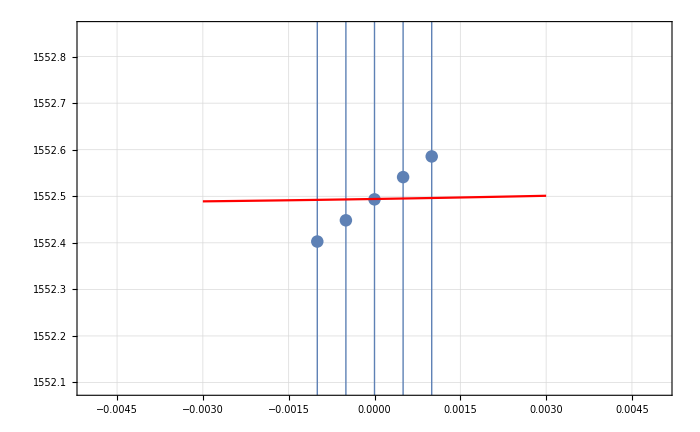
{{{1552.4,1552.45,1552.49,1552.54,1552.59},{4.95418,4.95425,4.95433,4.9544,4.95447}},b0 =  | -0.01
FittedModel[1552.48+100. (0.01+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.01 | 529.871 | -0.0000188725 | 0.999987
scale | 100. | 5.2964×10^6 | 0.0000188807 | 0.999987
yoffset | 1552.48 | 527.926 | 2.94072 | 0.098796 | 
 | DF | SS | MS
Model | 3 | 490976. | 163659.
Error | 2 | 0.000819171 | 0.000409585
Uncorrected Total | 5 | 490976. | 
Corrected Total | 4 | 0.000856113 |  | ,-Graphics-}

```mathematica
TransferToMCParableFit[DetTable[[All,3]],TransferDataList,bList]
```